```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
-∫_(-∞)^∞ (((ⅇ^(-x^2/2))/(√(2 π)))Log[(ⅇ^(-x^2/2))/(√(2 π))])ⅆx
```

1/2 (1-Log[1/(2 π)])

```mathematica
N[1/2 (1-Log[1/(2 π)])]
```

1.41894

```mathematica
ϕ==1/(1+ϕ)
```

ϕ==1/(1+ϕ)

```mathematica
Reduce[ϕ==1/(1+ϕ)]
```

ϕ==1/2 (-1-√5)||ϕ==1/2 (-1+√5)

```mathematica
N[1/2 (-1+√5)]
```

0.618034

```mathematica
Expectation[x, x\[Distributed]NormalDistribution[μ,σ^2]]
```

μ

```mathematica
Expectation[2x, x\[Distributed]NormalDistribution[μ,σ^2]]
```

2 μ

```mathematica
Expectation[x^2, x\[Distributed]NormalDistribution[μ,σ^2]]
```

μ^2+σ^4

```mathematica
{t^2,t(t^2-1)}
```

{t^2,t (-1+t^2)}

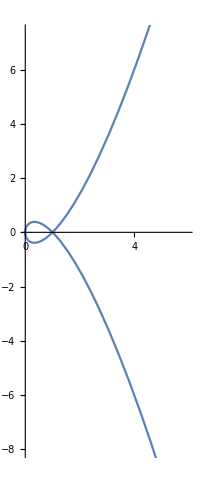

```mathematica
ParametricPlot[{t^2,t (-1+t^2)},{t,-2.449489742783178,2.449489742783178}]
```

```mathematica
FullSimplify[
Normalize@{t^2,t(t^2-1)}, t∈Reals]
```

{Abs[t]/(√(1-t^2+t^4)),(t (-1+t^2))/(√(t^2-t^4+t^6))}

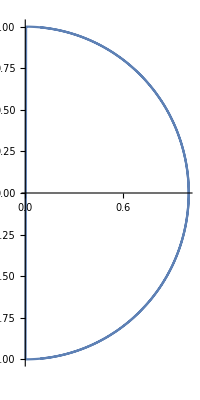

```mathematica
ParametricPlot[{Abs[t]/(√(1-t^2+t^4)),(t (-1+t^2))/(√(t^2-t^4+t^6))},{t,-10.920000000000007,10.920000000000007}]
```

```mathematica
FullSimplify[
Normalized[D[{t^2,t(t^2-1)},t]], t∈Reals]
```

Normalized[{2 t,-1+3 t^2}]

```mathematica
Normalized[D[{t^2,t(t^2-1)},t]]
```

Normalized[{2 t,-1+3 t^2}]

```mathematica
D[{t^2,t(t^2-1)},t]
```

{2 t,-1+3 t^2}

```mathematica
FullSimplify[
Normalized[
D[{t^2,t(t^2-1)},t]],
t∈Reals]
```

Normalized[{2 t,-1+3 t^2}]

```mathematica
{2 t,-1+3 t^2}
```

```mathematica
FullSimplify[
Normalize[{2 t,-1+3 t^2}],
t∈Reals]
```

{(2 t)/(√(1-2 t^2+9 t^4)),(-1+3 t^2)/(√(1-2 t^2+9 t^4))}

```mathematica
FullSimplify[
Normalize[
D[{t^2,t(t^2-1)},t]],
t∈Reals]
```

{(2 t)/(√(1-2 t^2+9 t^4)),(-1+3 t^2)/(√(1-2 t^2+9 t^4))}

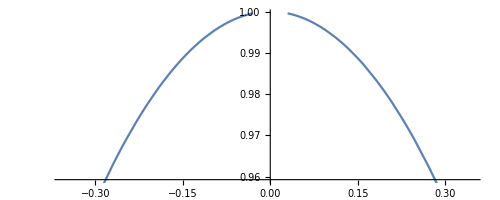

```mathematica
ParametricPlot[{(2 t)/(√(1-2 t^2+9 t^4)),(-1+3 t^2)/(√(1-2 t^2+9 t^4))},{t,-22.44666666666667,22.44666666666667}]
```

```mathematica
FullSimplify[
Integrate[
Normalize[
D[{t^2,t(t^2-1)},t]], t],
t∈Reals]
```

{1/3 ArcSinh[(-1+9 t^2)/(2 √2)],∫(-1+3 t^2)/(√(4 Abs[t]^2+Abs[-1+3 t^2]^2))ⅆt}

```mathematica
{t, t t}
```

{t,t^2}

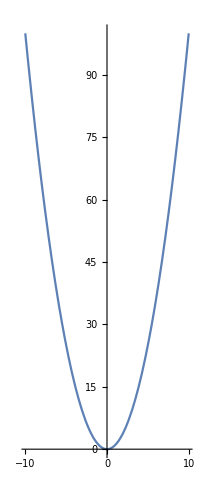

```mathematica
ParametricPlot[{t,t^2},{t,-10,10}]
```

```mathematica
{Sin[t], Cos[t]}
```

{Sin[t],Cos[t]}

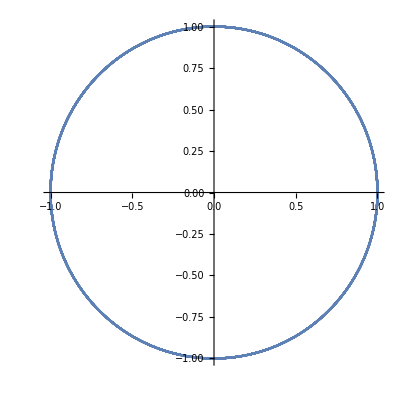

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,-26.389378290154262,26.389378290154262}]
```

```mathematica
{Cos[t],Sin[t]}
```

{Cos[t],Sin[t]}

```mathematica
Integrate[Normalize[D[{Cos[t],Sin[t]}, t]], t]
```

{-∫Sin[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2))ⅆt,∫Cos[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2))ⅆt}

```mathematica
Integrate[FullSimplify[
Normalize[D[{Cos[t],Sin[t]}, t]], t∈Reals],t]
```

{Cos[t],Sin[t]}

```mathematica
x[t]^2+y[t]^2==1
```

x[t]^2+y[t]^2==1

```mathematica
FindInstance[x[t]^2+y[t]^2==1,{t}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[x[t]^2+y[t]^2==1,{t}]

```mathematica
RotationMatrix[π/4]
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
{t,(1+Cos[π t])/2}.{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}
```

{t/(√2)+(1+Cos[π t])/(2 √2),-t/(√2)+(1+Cos[π t])/(2 √2)}

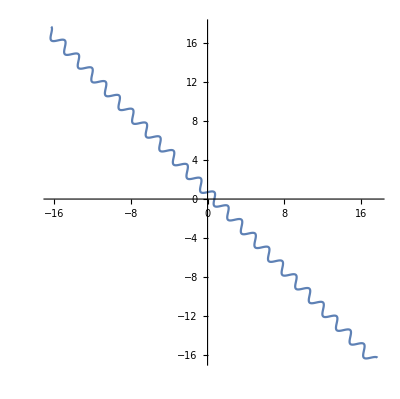

```mathematica
ParametricPlot[{t/(√2)+(1+Cos[π t])/(2 √2),-t/(√2)+(1+Cos[π t])/(2 √2)},{t,-24.,24.}]
```

```mathematica
π+π/4
```

(5 π)/4

```mathematica
RotationMatrix[(5 π)/4]
```

{{-1/(√2),1/(√2)},{-1/(√2),-1/(√2)}}

```mathematica
{t,(1+Cos[π t])/2}.{{-1/(√2),1/(√2)},{-1/(√2),-1/(√2)}}
```

{-t/(√2)-(1+Cos[π t])/(2 √2),t/(√2)-(1+Cos[π t])/(2 √2)}

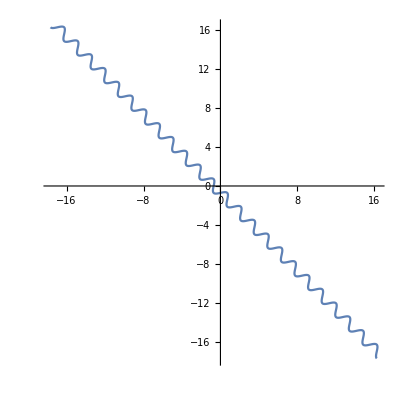

```mathematica
ParametricPlot[{-t/(√2)-(1+Cos[π t])/(2 √2),t/(√2)-(1+Cos[π t])/(2 √2)},{t,-24.,24.}]
```

```mathematica
D[{-t/(√2)-(1+Cos[π t])/(2 √2),t/(√2)-(1+Cos[π t])/(2 √2)},t]
```

{-1/(√2)+(π Sin[π t])/(2 √2),1/(√2)+(π Sin[π t])/(2 √2)}

```mathematica
Normalize[{-1/(√2)+(π Sin[π t])/(2 √2),1/(√2)+(π Sin[π t])/(2 √2)}]
```

{(-1/(√2)+(π Sin[π t])/(2 √2))/(√(Abs[-1/(√2)+(π Sin[π t])/(2 √2)]^2+Abs[1/(√2)+(π Sin[π t])/(2 √2)]^2)),(1/(√2)+(π Sin[π t])/(2 √2))/(√(Abs[-1/(√2)+(π Sin[π t])/(2 √2)]^2+Abs[1/(√2)+(π Sin[π t])/(2 √2)]^2))}

```mathematica
FullSimplify[
Normalize[{-1/(√2)+(π Sin[π t])/(2 √2),1/(√2)+(π Sin[π t])/(2 √2)}], t∈Reals]
```

{(-2+π Sin[π t])/(√(8+π^2-π^2 Cos[2 π t])),(2+π Sin[π t])/(√(8+π^2-π^2 Cos[2 π t]))}

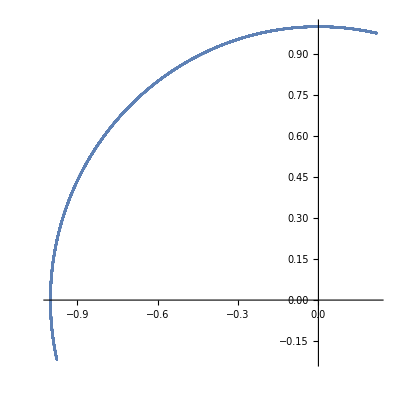

```mathematica
ParametricPlot[{(-2+π Sin[π t])/(√(8+π^2-π^2 Cos[2 π t])),(2+π Sin[π t])/(√(8+π^2-π^2 Cos[2 π t]))},{t,-6 π,6 π}]
```

```mathematica
Integrate[{(-2+π Sin[π t])/(√(8+π^2-π^2 Cos[2 π t])),(2+π Sin[π t])/(√(8+π^2-π^2 Cos[2 π t]))},t]
```

{-(EllipticF[π t,-π^2/4]-ⅈ Log[ⅈ √2 π Cos[π t]+√(8+π^2-π^2 Cos[2 π t])])/(√2 π),(EllipticF[π t,-π^2/4]+ⅈ Log[ⅈ √2 π Cos[π t]+√(8+π^2-π^2 Cos[2 π t])])/(√2 π)}

```mathematica
ParametricPlot[{-(EllipticF[π t,-π^2/4]-ⅈ Log[ⅈ √2 π Cos[π t]+√(8+π^2-π^2 Cos[2 π t])])/(√2 π),(EllipticF[π t,-π^2/4]+ⅈ Log[ⅈ √2 π Cos[π t]+√(8+π^2-π^2 Cos[2 π t])])/(√2 π)},{t,-8.586027226125697,8.586027226125697}]
```

-Graphics-

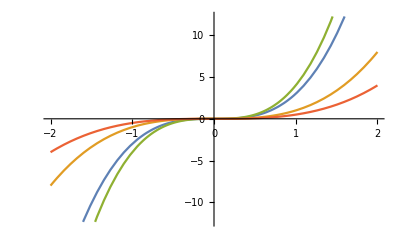

```mathematica
Plot[{3 x^3, x^3, 4 x^3, x^3/2}, {x, -2, 2}]
```

```mathematica
{t, t^2}
```

{t,t^2}

```mathematica
ParametricPlot[{t,t^2},{t,-10,10}]
```

-Graphics-

```mathematica
D[{t,t^2},t]
```

{1,2 t}

```mathematica
Normalize[{1,2 t}]
```

{1/(√(1+4 Abs[t]^2)),(2 t)/(√(1+4 Abs[t]^2))}

```mathematica
FullSimplify[
Normalize[{1,2 t}], t∈Reals]
```

{1/(√(1+4 t^2)),(2 t)/(√(1+4 t^2))}

```mathematica
Integrate[{1/(√(1+4 t^2)),(2 t)/(√(1+4 t^2))},t]
```

{1/2 ArcSinh[2 t],1/2 √(1+4 t^2)}

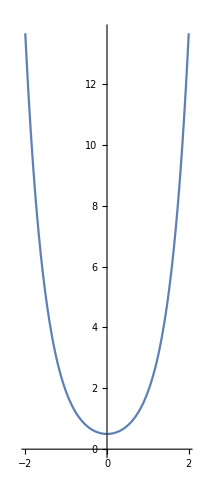

```mathematica
ParametricPlot[{1/2 ArcSinh[2 t],1/2 √(1+4 t^2)},{t,-13.649999999999999,13.649999999999999}]
```

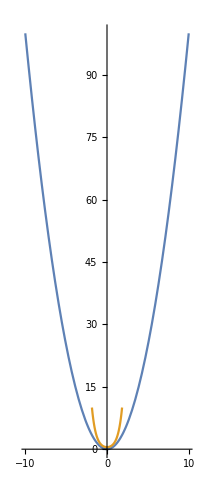

```mathematica
ParametricPlot[{
{t,t^2},
{1/2 ArcSinh[2 t],1/2 √(1+4 t^2)}},{t,-10,10}]
```

```mathematica
Ceiling[x]
```

Ceiling[x]

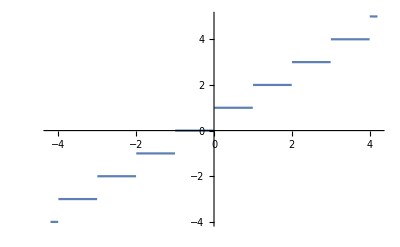

```mathematica
Plot[Ceiling[x],{x,-4.2,4.2}]
```

```mathematica
f[x]==x
3f[x/3]
```

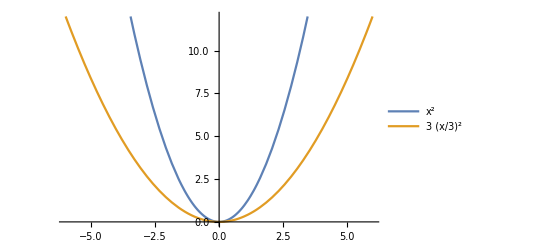

```mathematica
Plot[{x^2,3(x/3)^2}, {x, -6,6}, PlotLegends->"Expressions", PlotRange->{0,12}]
```

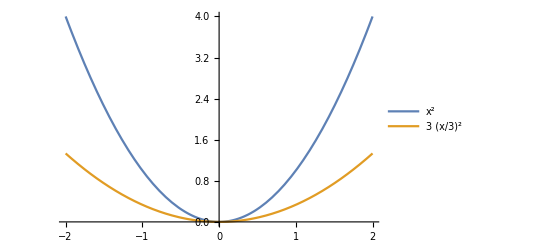

```mathematica
Plot[{x^2,3(x/3)^2}, {x, -2,2}, PlotLegends->"Expressions", PlotRange->{0,4}]
```

```mathematica
Manipulate[
Plot[{x^2,a(x/a)^2}, {x, -2,2}, PlotLegends->"Expressions"],
{a, 1, 3, 1}]
```

```mathematica
g[f[x],α]==SuperStar[f][x]
```

```mathematica
g[x^2,3]==3 (x/3)^2
```

```mathematica
Integrate[
FullSimplify[
Normalize[D[{x, x^2},x]], x∈Reals],x]
```

{1/2 ArcSinh[2 x],1/2 √(1+4 x^2)}

```mathematica
3 Integrate[
FullSimplify[
Normalize[D[{x, x^2},x]], x∈Reals],x]
```

{3/2 ArcSinh[2 x],3/2 √(1+4 x^2)}

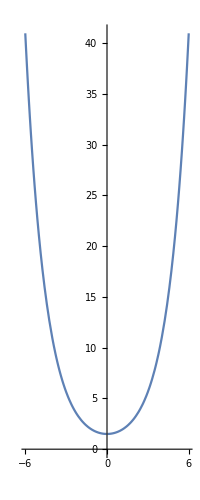

```mathematica
ParametricPlot[{3/2 ArcSinh[2 x],3/2 √(1+4 x^2)},{x,-13.649999999999999,13.649999999999999}]
```

```mathematica
{x, 3(x/3)^2}/.x->3
```

{3,3}

```mathematica
{3/2 ArcSinh[2 x],3/2 √(1+4 x^2)}/.x->3
```

{(3 ArcSinh[6])/2,(3 √37)/2}

```mathematica
N[{(3 ArcSinh[6])/2,(3 √37)/2}]
```

{3.73767,9.12414}

```mathematica
Manipulate[
ParametricPlot[α{3/2 ArcSinh[2 x],3/2 √(1+4 x^2)},{x,-3,3}],
{α, 1, 3, 1}]
```

```mathematica
Manipulate[
ParametricPlot[{
α{3/2 ArcSinh[2 x],3/2 √(1+4 x^2)},
{x, x^2}},{x,-3,3}],
{α, 1, 3, 1}]
```

```mathematica
FullSimplify[
Normalize[{t, t^2}], t∈Reals]
```

{t/(√(t^2+t^4)),Abs[t]/(√(1+t^2))}

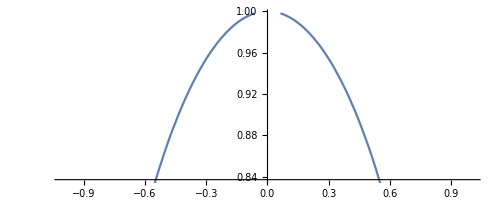

```mathematica
ParametricPlot[{t/(√(t^2+t^4)),Abs[t]/(√(1+t^2))},{t,-15.77333333333333,15.77333333333333}]
```

```mathematica
PDF[NormalDistribution[μ, σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
-∫_(-∞)^∞ ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)Log[(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)])ⅆx
```

$Aborted

```mathematica
-∫_(-∞)^∞ f[x]Log[f[x]]ⅆx
```

-∫_(-∞)^∞ f[x] Log[f[x]]ⅆx

```mathematica
Entropy[{a,b,c}]
```

Log[3]

```mathematica
Entropy[{a,b,c,d}]
```

Log[4]

```mathematica
Entropy[{a,b,c,d, e}]
```

Log[5]

```mathematica
Entropy[Range[10]]
```

Log[10]

```mathematica
-∫_0^1 f[x]Log[f[x]]ⅆx==λ f[x]
```

-∫_0^1 f[x] Log[f[x]]ⅆx==λ f[x]

```mathematica
-∫_0^1 f'[x]Log[f'[x]]ⅆx==λ f'[x]
```

-∫_0^1 Log[f'[x]] f'[x]ⅆx==λ f'[x]

```mathematica
DSolve[-∫_0^1 Log[f'[x]] f'[x]ⅆx==λ f'[x],{f[x]},{x}]
```

DSolve[-∫_0^1 Log[f'[x]] f'[x]ⅆx==λ f'[x],{f[x]},{x}]

```mathematica
TranslationTransform[{a,b}]
```

TransformationFunction[(1 | 0 | a
0 | 1 | b
0 | 0 | 1)]

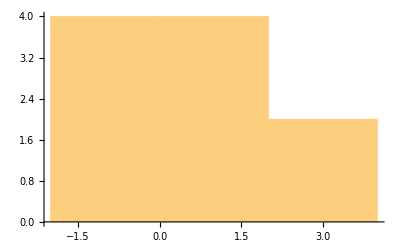

```mathematica
Histogram[RandomVariate[NormalDistribution[], 10]]
```

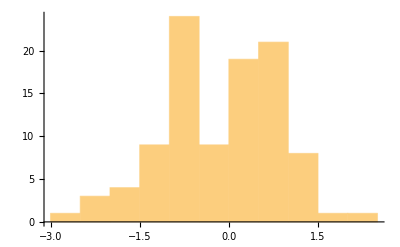

```mathematica
Histogram[RandomVariate[NormalDistribution[], 100]]
```

```mathematica
Manipulate[
Histogram[RandomVariate[NormalDistribution[], a]],
{a, 1, 10000,1}]
```

```mathematica
Plot3D[PDF[DirichletDistribution[{2,3,4}],{x,y}],{x,0,3/5},{y,0,3/5},RegionFunction->Function[{x,y,z},x^2+y^2<1/4&&x+y<6/7],Mesh->None,PlotStyle->Opacity[0.7],Filling->Bottom]
```

-Graphics3D-

```mathematica
FindDistribution[Map[Last,FinancialData["NASDAQ:AMZN", "Price", All]]]
```

ClearAll::wrsym: Symbol FinancialData is Protected.

Set::write: Tag FinancialData in Options[FinancialData] is Protected.

OptionValue::optnf: Option name Method not found in defaults for FinancialData.

MixtureDistribution[{0.845085,0.154915},{LogNormalDistribution[4.10114,1.53403],UniformDistribution[{1.32933,2039.57}]}]

```mathematica
StandardDeviation[MixtureDistribution[{0.8450850211631245,0.15491497883687555},{LogNormalDistribution[4.101142427727217,1.534026265117049],UniformDistribution[{1.3293289603702165,2039.5732571819829}]}]]
```

671.912

```mathematica
Median[MixtureDistribution[{0.8450850211631245,0.15491497883687555},{LogNormalDistribution[4.101142427727217,1.534026265117049],UniformDistribution[{1.3293289603702165,2039.5732571819829}]}]]
```

83.7247

```mathematica
Mean[MixtureDistribution[{0.8450850211631245,0.15491497883687555},{LogNormalDistribution[4.101142427727217,1.534026265117049],UniformDistribution[{1.3293289603702165,2039.5732571819829}]}]]
```

323.661

```mathematica
PDF[MixtureDistribution[{0.8450850211631245,0.15491497883687555},{LogNormalDistribution[4.101142427727217,1.534026265117049],UniformDistribution[{1.3293289603702165,2039.5732571819829}]}],x]
```

Piecewise[{{0., x≤0}, {0.+(0.219775 ⅇ^(-0.212473 (-4.10114+Log[x])^2))/x, 0<x<1.32933||x>2039.57}, {0.0000760041+(0.219775 ⅇ^(-0.212473 (-4.10114+Log[x])^2))/x, True}}]

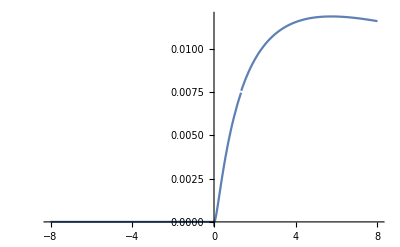

```mathematica
Plot[%98,{x,-8,8}]
```

```mathematica
Trace[1+1]
```

{1+1,2}

```mathematica
Trace[FindDistribution[Map[Last,FinancialData["NASDAQ:AMZN", "Price", All]]]]
```

OptionValue::optnf: Option name Method not found in defaults for FinancialData.

$Aborted[]

```mathematica
1+1
```

2

```mathematica
Trace[∫x^2 ⅆx]
```

{∫x^2 ⅆx,x^3/3}

```mathematica
Trace[1+∫x^2 ⅆx]
```

{{∫x^2 ⅆx,x^3/3},1+x^3/3}

```mathematica
Trace@Mean[RandomVariate[NormalDistribution[],100]]
```

{{{NormalDistribution[],NormalDistribution[0,1]},RandomVariate[NormalDistribution[0,1],100],{-1.18965,-1.27804,-0.389242,0.0367856,-0.0977782,-0.828153,-0.0774545,-0.564918,0.736188,0.839765,-0.384904,-0.547827,-0.583931,-1.69502,-0.703527,-0.67973,-0.222228,-0.908137,-0.863089,0.458557,-0.438666,-0.144888,0.60896,0.495096,-0.0724897,-1.25777,-0.359711,0.147053,1.4555,1.39373,-0.277691,1.64345,-0.764611,0.38684,-0.19294,0.442452,0.622082,1.13515,-0.225325,-0.176042,0.532597,-0.111939,-1.35093,0.684009,0.135425,0.196999,0.356218,-1.79196,0.512085,-0.227236,-1.02657,0.696852,2.03241,-1.3213,0.153554,1.12644,-2.4346,-0.684357,-0.739762,-0.255858,-1.89438,-0.287214,-0.19186,0.450696,-0.372222,0.000723871,1.82574,-1.29879,-1.22735,1.46277,0.445139,0.343219,-1.69328,0.221348,-0.195104,-2.64257,0.855338,-1.43986,0.791937,-0.728348,-0.34911,0.936526,0.106859,1.30656,-0.962681,-2.23584,0.570757,-1.24165,-0.928782,1.80381,-0.28472,-0.179237,-0.71831,0.135579,0.307658,0.48095,-0.702894,0.366691,-0.220871,-1.48489}},Mean[{-1.18965,-1.27804,-0.389242,0.0367856,-0.0977782,-0.828153,-0.0774545,-0.564918,0.736188,0.839765,-0.384904,-0.547827,-0.583931,-1.69502,-0.703527,-0.67973,-0.222228,-0.908137,-0.863089,0.458557,-0.438666,-0.144888,0.60896,0.495096,-0.0724897,-1.25777,-0.359711,0.147053,1.4555,1.39373,-0.277691,1.64345,-0.764611,0.38684,-0.19294,0.442452,0.622082,1.13515,-0.225325,-0.176042,0.532597,-0.111939,-1.35093,0.684009,0.135425,0.196999,0.356218,-1.79196,0.512085,-0.227236,-1.02657,0.696852,2.03241,-1.3213,0.153554,1.12644,-2.4346,-0.684357,-0.739762,-0.255858,-1.89438,-0.287214,-0.19186,0.450696,-0.372222,0.000723871,1.82574,-1.29879,-1.22735,1.46277,0.445139,0.343219,-1.69328,0.221348,-0.195104,-2.64257,0.855338,-1.43986,0.791937,-0.728348,-0.34911,0.936526,0.106859,1.30656,-0.962681,-2.23584,0.570757,-1.24165,-0.928782,1.80381,-0.28472,-0.179237,-0.71831,0.135579,0.307658,0.48095,-0.702894,0.366691,-0.220871,-1.48489}],-0.169077}

```mathematica
RotationTransform[θ]
```

TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]

```mathematica
TransformationMatrix[TransformationFunction[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]
```

{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}

```mathematica
FullForm[TransformationFunction[({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})]]
```

TransformationFunction[List[List[Cos[\[Theta]],Times[-1,Sin[\[Theta]]],0],List[Sin[\[Theta]],Cos[\[Theta]],0],List[0,0,1]]]

```mathematica
RotationTransform[θ]//Trace
```

{RotationTransform[θ],{{System`TransformConstructorDump`scalarQ,!MatchQ[#1,_List|_SparseArray]&},(!MatchQ[#1,_List|_SparseArray]&)[θ],!MatchQ[θ,_List|_SparseArray],{MatchQ[θ,_List|_SparseArray],False},!False,True},{VectorQ[{0,0}]&&Length[{0,0}]==2,{VectorQ[{0,0}],True},{{Length[{0,0}],2},2==2,True},True},RotationTransform[θ,{{1,0},{0,1}},{0,0}],{{System`TransformConstructorDump`scalarQ,!MatchQ[#1,_List|_SparseArray]&},(!MatchQ[#1,_List|_SparseArray]&)[θ],!MatchQ[θ,_List|_SparseArray],{MatchQ[θ,_List|_SparseArray],False},!False,True},{VectorQ[{1,0}],True},{VectorQ[{0,1}],True},{VectorQ[{0,0}],True},{System`TransformConstructorDump`vCompDim[RotationTransform,{{1,0},{0,0}}],Length[{1,0}]==Length[{0,0}]||System`TransformConstructorDump`vMessage[RotationTransform::idim,{1,0},{0,0}],{{Length[{1,0}],2},{Length[{0,0}],2},2==2,True},True},{Module[{System`TransformConstructorDump`M$=System`TransformConstructorDump`iRotationMatrix[RotationTransform,{θ,0,0},{{1,0},{0,1}}]},RuleCondition[$ConditionHold[$ConditionHold[System`TransformConstructorDump`postProcess[TranslationTransform[{0,0}].LinearFractionalTransform[{System`TransformConstructorDump`M$}].TranslationTransform[-{0,0}]]]],System`TransformConstructorDump`M$=!=$Failed]],{System`TransformConstructorDump`iRotationMatrix[RotationTransform,{θ,0,0},{{1,0},{0,1}}],Module[{System`TransformConstructorDump`M$,System`TransformConstructorDump`M2$,System`TransformConstructorDump`u$,System`TransformConstructorDump`v$,System`TransformConstructorDump`phi$,System`TransformConstructorDump`xi1$,System`TransformConstructorDump`xi2$,System`TransformConstructorDump`z11$,System`TransformConstructorDump`z12$,System`TransformConstructorDump`z21$,System`TransformConstructorDump`z22$,System`TransformConstructorDump`a$,System`TransformConstructorDump`b$,System`TransformConstructorDump`n$,System`TransformConstructorDump`prec$,System`TransformConstructorDump`method$,System`TransformConstructorDump`rc$=real},If[VectorQ[{{1,0},{0,1}}],If[Length[{{1,0},{0,1}}]≠3,Message[RotationTransform::v3d,{{1,0},{0,1}}];Return[$Failed]];If[System`TransformConstructorDump`smallQ[{{1,0},{0,1}}],Message[RotationTransform::idir,{{1,0},{0,1}}];Return[$Failed]];{System`TransformConstructorDump`phi$,System`TransformConstructorDump`xi1$,System`TransformConstructorDump`xi2$}={θ,0,0};System`TransformConstructorDump`M$=Quiet[System`TransformConstructorDump`iRotationMatrix[RotationTransform,{},{{0,0,1},{{1,0},{0,1}}}]];System`TransformConstructorDump`rc$=If[VectorQ[Flatten[System`TransformConstructorDump`M$],#1∈ℝ&],real,complex];System`TransformConstructorDump`M2$={{Cos[System`TransformConstructorDump`phi$],-Sin[System`TransformConstructorDump`phi$],0},{Sin[System`TransformConstructorDump`phi$],Cos[System`TransformConstructorDump`phi$],0},{0,0,1}};Return[System`TransformConstructorDump`postProcess[System`TransformConstructorDump`M$.System`TransformConstructorDump`M2$.System`TransformConstructorDump`conjtrans[System`TransformConstructorDump`M$,System`TransformConstructorDump`rc$]]]];{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$}={{1,0},{0,1}};System`TransformConstructorDump`n$=Length[System`TransformConstructorDump`u$];If[!System`TransformConstructorDump`vCompDim[RotationTransform,{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$}],Return[$Failed]];If[System`TransformConstructorDump`n$<2,Message[RotationTransform::rdim,System`TransformConstructorDump`u$];Return[$Failed]];(If[System`TransformConstructorDump`smallQ[#1],Message[RotationTransform::idir,#1];Return[$Failed,Module]]&)/@{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$};System`TransformConstructorDump`prec$=Precision[{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$}];System`TransformConstructorDump`rc$=If[VectorQ[Flatten[{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$}],#1∈ℝ&],real,complex];System`TransformConstructorDump`method$=Which[System`TransformConstructorDump`prec$=!=∞,Reorthogonalization,VectorQ[Flatten[{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$}],#1∈ℚ&],Automatic,True,Householder];System`TransformConstructorDump`M$=Orthogonalize[Join@@{{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$},NullSpace[System`TransformConstructorDump`conj[{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$},System`TransformConstructorDump`rc$]]},Method→System`TransformConstructorDump`method$];If[Length[System`TransformConstructorDump`M$]>System`TransformConstructorDump`n$,If[{θ,0,0}==={}&&System`TransformConstructorDump`closeQ@@Normalize/@{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$},Return[SetPrecision[IdentityMatrix[System`TransformConstructorDump`n$],System`TransformConstructorDump`prec$]]];If[System`TransformConstructorDump`n$>2,Message[RotationTransform::spln,System`TransformConstructorDump`u$,System`TransformConstructorDump`v$],If[{θ,0,0}=!={},Message[RotationTransform::sdir,System`TransformConstructorDump`u$,System`TransformConstructorDump`v$]]]];System`TransformConstructorDump`M$=Select[System`TransformConstructorDump`M$,!System`TransformConstructorDump`smallQ[#1]&,System`TransformConstructorDump`n$];If[Length[System`TransformConstructorDump`M$]≠System`TransformConstructorDump`n$,Return[$Failed]];If[{θ,0,0}==={},{{System`TransformConstructorDump`z11$,System`TransformConstructorDump`z12$},{System`TransformConstructorDump`z21$,System`TransformConstructorDump`z22$}}=Take[{System`TransformConstructorDump`u$,System`TransformConstructorDump`v$}.System`TransformConstructorDump`conjtrans[System`TransformConstructorDump`M$,System`TransformConstructorDump`rc$],2,2];{System`TransformConstructorDump`a$,System`TransformConstructorDump`b$}={System`TransformConstructorDump`conj[System`TransformConstructorDump`z11$,System`TransformConstructorDump`rc$] System`TransformConstructorDump`z21$,-System`TransformConstructorDump`z11$ System`TransformConstructorDump`conj[System`TransformConstructorDump`z22$,System`TransformConstructorDump`rc$]};System`TransformConstructorDump`M2$={{System`TransformConstructorDump`a$,System`TransformConstructorDump`b$},{-System`TransformConstructorDump`conj[System`TransformConstructorDump`b$,System`TransformConstructorDump`rc$],System`TransformConstructorDump`conj[System`TransformConstructorDump`a$,System`TransformConstructorDump`rc$]}}/(System`TransformConstructorDump`norm[System`TransformConstructorDump`u$,System`TransformConstructorDump`rc$] System`TransformConstructorDump`norm[System`TransformConstructorDump`v$,System`TransformConstructorDump`rc$]);,{System`TransformConstructorDump`phi$,System`TransformConstructorDump`xi1$,System`TransformConstructorDump`xi2$}={θ,0,0};System`TransformConstructorDump`M2$={{Cos[System`TransformConstructorDump`phi$] ⅇ^(ⅈ System`TransformConstructorDump`xi1$),-Sin[System`TransformConstructorDump`phi$] ⅇ^(ⅈ System`TransformConstructorDump`xi2$)},{Sin[System`TransformConstructorDump`phi$] ⅇ^(-ⅈ System`TransformConstructorDump`xi2$),Cos[System`TransformConstructorDump`phi$] ⅇ^(-ⅈ System`TransformConstructorDump`xi1$)}}];If[System`TransformConstructorDump`n$>2,System`TransformConstructorDump`M2$=ArrayFlatten[{{System`TransformConstructorDump`M2$,0},{0,IdentityMatrix[System`TransformConstructorDump`n$-2]}}]];System`TransformConstructorDump`postProcess[Transpose[System`TransformConstructorDump`M$].System`TransformConstructorDump`M2$.System`TransformConstructorDump`conj[System`TransformConstructorDump`M$,System`TransformConstructorDump`rc$]]],{System`TransformConstructorDump`rc$226757=real,real},{If[VectorQ[{{1,0},{0,1}}],If[Length[{{1,0},{0,1}}]≠3,Message[RotationTransform::v3d,{{1,0},{0,1}}];Return[$Failed]];If[System`TransformConstructorDump`smallQ[{{1,0},{0,1}}],Message[RotationTransform::idir,{{1,0},{0,1}}];Return[$Failed]];{System`TransformConstructorDump`phi$226757,System`TransformConstructorDump`xi1$226757,System`TransformConstructorDump`xi2$226757}={θ,0,0};System`TransformConstructorDump`M$226757=Quiet[System`TransformConstructorDump`iRotationMatrix[RotationTransform,{},{{0,0,1},{{1,0},{0,1}}}]];System`TransformConstructorDump`rc$226757=If[VectorQ[Flatten[System`TransformConstructorDump`M$226757],#1∈ℝ&],real,complex];System`TransformConstructorDump`M2$226757={{Cos[System`TransformConstructorDump`phi$226757],-Sin[System`TransformConstructorDump`phi$226757],0},{Sin[System`TransformConstructorDump`phi$226757],Cos[System`TransformConstructorDump`phi$226757],0},{0,0,1}};Return[System`TransformConstructorDump`postProcess[System`TransformConstructorDump`M$226757.System`TransformConstructorDump`M2$226757.System`TransformConstructorDump`conjtrans[System`TransformConstructorDump`M$226757,System`TransformConstructorDump`rc$226757]]]];{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757}={{1,0},{0,1}};System`TransformConstructorDump`n$226757=Length[System`TransformConstructorDump`u$226757];If[!System`TransformConstructorDump`vCompDim[RotationTransform,{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757}],Return[$Failed]];If[System`TransformConstructorDump`n$226757<2,Message[RotationTransform::rdim,System`TransformConstructorDump`u$226757];Return[$Failed]];(If[System`TransformConstructorDump`smallQ[#1],Message[RotationTransform::idir,#1];Return[$Failed,Module]]&)/@{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757};System`TransformConstructorDump`prec$226757=Precision[{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757}];System`TransformConstructorDump`rc$226757=If[VectorQ[Flatten[{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757}],#1∈ℝ&],real,complex];System`TransformConstructorDump`method$226757=Which[System`TransformConstructorDump`prec$226757=!=∞,Reorthogonalization,VectorQ[Flatten[{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757}],#1∈ℚ&],Automatic,True,Householder];System`TransformConstructorDump`M$226757=Orthogonalize[Join@@{{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757},NullSpace[System`TransformConstructorDump`conj[{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757},System`TransformConstructorDump`rc$226757]]},Method→System`TransformConstructorDump`method$226757];If[Length[System`TransformConstructorDump`M$226757]>System`TransformConstructorDump`n$226757,If[{θ,0,0}==={}&&System`TransformConstructorDump`closeQ@@Normalize/@{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757},Return[SetPrecision[IdentityMatrix[System`TransformConstructorDump`n$226757],System`TransformConstructorDump`prec$226757]]];If[System`TransformConstructorDump`n$226757>2,Message[RotationTransform::spln,System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757],If[{θ,0,0}=!={},Message[RotationTransform::sdir,System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757]]]];System`TransformConstructorDump`M$226757=Select[System`TransformConstructorDump`M$226757,!System`TransformConstructorDump`smallQ[#1]&,System`TransformConstructorDump`n$226757];If[Length[System`TransformConstructorDump`M$226757]≠System`TransformConstructorDump`n$226757,Return[$Failed]];If[{θ,0,0}==={},{{System`TransformConstructorDump`z11$226757,System`TransformConstructorDump`z12$226757},{System`TransformConstructorDump`z21$226757,System`TransformConstructorDump`z22$226757}}=Take[{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757}.System`TransformConstructorDump`conjtrans[System`TransformConstructorDump`M$226757,System`TransformConstructorDump`rc$226757],2,2];{System`TransformConstructorDump`a$226757,System`TransformConstructorDump`b$226757}={System`TransformConstructorDump`conj[System`TransformConstructorDump`z11$226757,System`TransformConstructorDump`rc$226757] System`TransformConstructorDump`z21$226757,-System`TransformConstructorDump`z11$226757 System`TransformConstructorDump`conj[System`TransformConstructorDump`z22$226757,System`TransformConstructorDump`rc$226757]};System`TransformConstructorDump`M2$226757={{System`TransformConstructorDump`a$226757,System`TransformConstructorDump`b$226757},{-System`TransformConstructorDump`conj[System`TransformConstructorDump`b$226757,System`TransformConstructorDump`rc$226757],System`TransformConstructorDump`conj[System`TransformConstructorDump`a$226757,System`TransformConstructorDump`rc$226757]}}/(System`TransformConstructorDump`norm[System`TransformConstructorDump`u$226757,System`TransformConstructorDump`rc$226757] System`TransformConstructorDump`norm[System`TransformConstructorDump`v$226757,System`TransformConstructorDump`rc$226757]);,{System`TransformConstructorDump`phi$226757,System`TransformConstructorDump`xi1$226757,System`TransformConstructorDump`xi2$226757}={θ,0,0};System`TransformConstructorDump`M2$226757={{Cos[System`TransformConstructorDump`phi$226757] ⅇ^(ⅈ System`TransformConstructorDump`xi1$226757),-Sin[System`TransformConstructorDump`phi$226757] ⅇ^(ⅈ System`TransformConstructorDump`xi2$226757)},{Sin[System`TransformConstructorDump`phi$226757] ⅇ^(-ⅈ System`TransformConstructorDump`xi2$226757),Cos[System`TransformConstructorDump`phi$226757] ⅇ^(-ⅈ System`TransformConstructorDump`xi1$226757)}}];If[System`TransformConstructorDump`n$226757>2,System`TransformConstructorDump`M2$226757=ArrayFlatten[{{System`TransformConstructorDump`M2$226757,0},{0,IdentityMatrix[System`TransformConstructorDump`n$226757-2]}}]];System`TransformConstructorDump`postProcess[Transpose[System`TransformConstructorDump`M$226757].System`TransformConstructorDump`M2$226757.System`TransformConstructorDump`conj[System`TransformConstructorDump`M$226757,System`TransformConstructorDump`rc$226757]],{{VectorQ[{{1,0},{0,1}}],False},If[False,If[Length[{{1,0},{0,1}}]≠3,Message[RotationTransform::v3d,{{1,0},{0,1}}];Return[$Failed]];If[System`TransformConstructorDump`smallQ[{{1,0},{0,1}}],Message[RotationTransform::idir,{{1,0},{0,1}}];Return[$Failed]];{System`TransformConstructorDump`phi$226757,System`TransformConstructorDump`xi1$226757,System`TransformConstructorDump`xi2$226757}={θ,0,0};System`TransformConstructorDump`M$226757=Quiet[System`TransformConstructorDump`iRotationMatrix[RotationTransform,{},{{0,0,1},{{1,0},{0,1}}}]];System`TransformConstructorDump`rc$226757=If[VectorQ[Flatten[System`TransformConstructorDump`M$226757],#1∈ℝ&],real,complex];System`TransformConstructorDump`M2$226757={{Cos[System`TransformConstructorDump`phi$226757],-Sin[System`TransformConstructorDump`phi$226757],0},{Sin[System`TransformConstructorDump`phi$226757],Cos[System`TransformConstructorDump`phi$226757],0},{0,0,1}};Return[System`TransformConstructorDump`postProcess[System`TransformConstructorDump`M$226757.System`TransformConstructorDump`M2$226757.System`TransformConstructorDump`conjtrans[System`TransformConstructorDump`M$226757,System`TransformConstructorDump`rc$226757]]]],Null},{{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757}={{1,0},{0,1}},{{1,0},{0,1}}},{{{System`TransformConstructorDump`u$226757,{1,0}},Length[{1,0}],2},System`TransformConstructorDump`n$226757=2,2},{{{{{System`TransformConstructorDump`u$226757,{1,0}},{System`TransformConstructorDump`v$226757,{0,1}},{{1,0},{0,1}}},System`TransformConstructorDump`vCompDim[RotationTransform,{{1,0},{0,1}}],Length[{1,0}]==Length[{0,1}]||System`TransformConstructorDump`vMessage[RotationTransform::idim,{1,0},{0,1}],{{Length[{1,0}],2},{Length[{0,1}],2},2==2,True},True},!True,False},If[False,Return[$Failed]],Null},{{{System`TransformConstructorDump`n$226757,2},2<2,False},If[False,Message[RotationTransform::rdim,System`TransformConstructorDump`u$226757];Return[$Failed]],Null},{{{System`TransformConstructorDump`u$226757,{1,0}},{System`TransformConstructorDump`v$226757,{0,1}},{{1,0},{0,1}}},(If[System`TransformConstructorDump`smallQ[#1],Message[RotationTransform::idir,#1];Return[$Failed,Module]]&)/@{{1,0},{0,1}},{(If[System`TransformConstructorDump`smallQ[#1],Message[RotationTransform::idir,#1];Return[$Failed,Module]]&)[{1,0}],(If[System`TransformConstructorDump`smallQ[#1],Message[RotationTransform::idir,#1];Return[$Failed,Module]]&)[{0,1}]},{(If[System`TransformConstructorDump`smallQ[#1],Message[RotationTransform::idir,#1];Return[$Failed,Module]]&)[{1,0}],If[System`TransformConstructorDump`smallQ[{1,0}],Message[RotationTransform::idir,{1,0}];Return[$Failed,Module]],{{System`TransformConstructorDump`smallQ,Quiet[If[Precision[#1]=!=∞,TrueQ[Norm[#1]==0],PossibleZeroQ[Norm[#1]]]]&},(Quiet[If[Precision[#1]=!=∞,TrueQ[Norm[#1]==0],PossibleZeroQ[Norm[#1]]]]&)[{1,0}],Quiet[If[Precision[{1,0}]=!=∞,TrueQ[Norm[{1,0}]==0],PossibleZeroQ[Norm[{1,0}]]]],{{{Precision[{1,0}],∞},{∞,∞},∞=!=∞,False},If[False,TrueQ[Norm[{1,0}]==0],PossibleZeroQ[Norm[{1,0}]]],PossibleZeroQ[Norm[{1,0}]],{Norm[{1,0}],1},PossibleZeroQ[1],False},False},If[False,Message[RotationTransform::idir,{1,0}];Return[$Failed,Module]],Null},{(If[System`TransformConstructorDump`smallQ[#1],Message[RotationTransform::idir,#1];Return[$Failed,Module]]&)[{0,1}],If[System`TransformConstructorDump`smallQ[{0,1}],Message[RotationTransform::idir,{0,1}];Return[$Failed,Module]],{{System`TransformConstructorDump`smallQ,Quiet[If[Precision[#1]=!=∞,TrueQ[Norm[#1]==0],PossibleZeroQ[Norm[#1]]]]&},(Quiet[If[Precision[#1]=!=∞,TrueQ[Norm[#1]==0],PossibleZeroQ[Norm[#1]]]]&)[{0,1}],Quiet[If[Precision[{0,1}]=!=∞,TrueQ[Norm[{0,1}]==0],PossibleZeroQ[Norm[{0,1}]]]],{{{Precision[{0,1}],∞},{∞,∞},∞=!=∞,False},If[False,TrueQ[Norm[{0,1}]==0],PossibleZeroQ[Norm[{0,1}]]],PossibleZeroQ[Norm[{0,1}]],{Norm[{0,1}],1},PossibleZeroQ[1],False},False},If[False,Message[RotationTransform::idir,{0,1}];Return[$Failed,Module]],Null},{Null,Null}},{{{{System`TransformConstructorDump`u$226757,{1,0}},{System`TransformConstructorDump`v$226757,{0,1}},{{1,0},{0,1}}},Precision[{{1,0},{0,1}}],∞},System`TransformConstructorDump`prec$226757=∞,∞},{{{{{{System`TransformConstructorDump`u$226757,{1,0}},{System`TransformConstructorDump`v$226757,{0,1}},{{1,0},{0,1}}},Flatten[{{1,0},{0,1}}],{1,0,0,1}},VectorQ[{1,0,0,1},#1∈ℝ&],{(#1∈ℝ&)[1],1∈ℝ,True},{(#1∈ℝ&)[0],0∈ℝ,True},{(#1∈ℝ&)[0],0∈ℝ,True},{(#1∈ℝ&)[1],1∈ℝ,True},True},If[True,real,complex],real},System`TransformConstructorDump`rc$226757=real,real},{{Which[System`TransformConstructorDump`prec$226757=!=∞,Reorthogonalization,VectorQ[Flatten[{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757}],#1∈ℚ&],Automatic,True,Householder],{{System`TransformConstructorDump`prec$226757,∞},{∞,∞},∞=!=∞,False},{{{{System`TransformConstructorDump`u$226757,{1,0}},{System`TransformConstructorDump`v$226757,{0,1}},{{1,0},{0,1}}},Flatten[{{1,0},{0,1}}],{1,0,0,1}},VectorQ[{1,0,0,1},#1∈ℚ&],{(#1∈ℚ&)[1],1∈ℚ,True},{(#1∈ℚ&)[0],0∈ℚ,True},{(#1∈ℚ&)[0],0∈ℚ,True},{(#1∈ℚ&)[1],1∈ℚ,True},True},Automatic},System`TransformConstructorDump`method$226757=Automatic,Automatic},{{{{{{System`TransformConstructorDump`u$226757,{1,0}},{System`TransformConstructorDump`v$226757,{0,1}},{{1,0},{0,1}}},{{{{System`TransformConstructorDump`u$226757,{1,0}},{System`TransformConstructorDump`v$226757,{0,1}},{{1,0},{0,1}}},{System`TransformConstructorDump`rc$226757,real},System`TransformConstructorDump`conj[{{1,0},{0,1}},real],{{1,0},{0,1}}},NullSpace[{{1,0},{0,1}}],{}},{{{1,0},{0,1}},{}}},Join@@{{{1,0},{0,1}},{}},Join[{{1,0},{0,1}},{}],{{1,0},{0,1}}},{{System`TransformConstructorDump`method$226757,Automatic},Method→Automatic,Method→Automatic},Orthogonalize[{{1,0},{0,1}},Method→Automatic],{{1,0},{0,1}}},System`TransformConstructorDump`M$226757={{1,0},{0,1}},{{1,0},{0,1}}},{{{{System`TransformConstructorDump`M$226757,{{1,0},{0,1}}},Length[{{1,0},{0,1}}],2},{System`TransformConstructorDump`n$226757,2},2>2,False},If[False,If[{θ,0,0}==={}&&System`TransformConstructorDump`closeQ@@Normalize/@{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757},Return[SetPrecision[IdentityMatrix[System`TransformConstructorDump`n$226757],System`TransformConstructorDump`prec$226757]]];If[System`TransformConstructorDump`n$226757>2,Message[RotationTransform::spln,System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757],If[{θ,0,0}=!={},Message[RotationTransform::sdir,System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757]]]],Null},{{{System`TransformConstructorDump`M$226757,{{1,0},{0,1}}},{System`TransformConstructorDump`n$226757,2},Select[{{1,0},{0,1}},!System`TransformConstructorDump`smallQ[#1]&,2],{(!System`TransformConstructorDump`smallQ[#1]&)[{1,0}],!System`TransformConstructorDump`smallQ[{1,0}],{{System`TransformConstructorDump`smallQ,Quiet[If[Precision[#1]=!=∞,TrueQ[Norm[#1]==0],PossibleZeroQ[Norm[#1]]]]&},(Quiet[If[Precision[#1]=!=∞,TrueQ[Norm[#1]==0],PossibleZeroQ[Norm[#1]]]]&)[{1,0}],Quiet[If[Precision[{1,0}]=!=∞,TrueQ[Norm[{1,0}]==0],PossibleZeroQ[Norm[{1,0}]]]],{{{Precision[{1,0}],∞},{∞,∞},∞=!=∞,False},If[False,TrueQ[Norm[{1,0}]==0],PossibleZeroQ[Norm[{1,0}]]],PossibleZeroQ[Norm[{1,0}]],{Norm[{1,0}],1},PossibleZeroQ[1],False},False},!False,True},{(!System`TransformConstructorDump`smallQ[#1]&)[{0,1}],!System`TransformConstructorDump`smallQ[{0,1}],{{System`TransformConstructorDump`smallQ,Quiet[If[Precision[#1]=!=∞,TrueQ[Norm[#1]==0],PossibleZeroQ[Norm[#1]]]]&},(Quiet[If[Precision[#1]=!=∞,TrueQ[Norm[#1]==0],PossibleZeroQ[Norm[#1]]]]&)[{0,1}],Quiet[If[Precision[{0,1}]=!=∞,TrueQ[Norm[{0,1}]==0],PossibleZeroQ[Norm[{0,1}]]]],{{{Precision[{0,1}],∞},{∞,∞},∞=!=∞,False},If[False,TrueQ[Norm[{0,1}]==0],PossibleZeroQ[Norm[{0,1}]]],PossibleZeroQ[Norm[{0,1}]],{Norm[{0,1}],1},PossibleZeroQ[1],False},False},!False,True},{{1,0},{0,1}}},System`TransformConstructorDump`M$226757={{1,0},{0,1}},{{1,0},{0,1}}},{{{{System`TransformConstructorDump`M$226757,{{1,0},{0,1}}},Length[{{1,0},{0,1}}],2},{System`TransformConstructorDump`n$226757,2},2≠2,False},If[False,Return[$Failed]],Null},{{{θ,0,0}==={},False},If[False,{{System`TransformConstructorDump`z11$226757,System`TransformConstructorDump`z12$226757},{System`TransformConstructorDump`z21$226757,System`TransformConstructorDump`z22$226757}}=Take[{System`TransformConstructorDump`u$226757,System`TransformConstructorDump`v$226757}.System`TransformConstructorDump`conjtrans[System`TransformConstructorDump`M$226757,System`TransformConstructorDump`rc$226757],2,2];{System`TransformConstructorDump`a$226757,System`TransformConstructorDump`b$226757}={System`TransformConstructorDump`conj[System`TransformConstructorDump`z11$226757,System`TransformConstructorDump`rc$226757] System`TransformConstructorDump`z21$226757,-System`TransformConstructorDump`z11$226757 System`TransformConstructorDump`conj[System`TransformConstructorDump`z22$226757,System`TransformConstructorDump`rc$226757]};System`TransformConstructorDump`M2$226757={{System`TransformConstructorDump`a$226757,System`TransformConstructorDump`b$226757},{-System`TransformConstructorDump`conj[System`TransformConstructorDump`b$226757,System`TransformConstructorDump`rc$226757],System`TransformConstructorDump`conj[System`TransformConstructorDump`a$226757,System`TransformConstructorDump`rc$226757]}}/(System`TransformConstructorDump`norm[System`TransformConstructorDump`u$226757,System`TransformConstructorDump`rc$226757] System`TransformConstructorDump`norm[System`TransformConstructorDump`v$226757,System`TransformConstructorDump`rc$226757]);,{System`TransformConstructorDump`phi$226757,System`TransformConstructorDump`xi1$226757,System`TransformConstructorDump`xi2$226757}={θ,0,0};System`TransformConstructorDump`M2$226757={{Cos[System`TransformConstructorDump`phi$226757] ⅇ^(ⅈ System`TransformConstructorDump`xi1$226757),-Sin[System`TransformConstructorDump`phi$226757] ⅇ^(ⅈ System`TransformConstructorDump`xi2$226757)},{Sin[System`TransformConstructorDump`phi$226757] ⅇ^(-ⅈ System`TransformConstructorDump`xi2$226757),Cos[System`TransformConstructorDump`phi$226757] ⅇ^(-ⅈ System`TransformConstructorDump`xi1$226757)}}],{System`TransformConstructorDump`phi$226757,System`TransformConstructorDump`xi1$226757,System`TransformConstructorDump`xi2$226757}={θ,0,0};System`TransformConstructorDump`M2$226757={{Cos[System`TransformConstructorDump`phi$226757] ⅇ^(ⅈ System`TransformConstructorDump`xi1$226757),-Sin[System`TransformConstructorDump`phi$226757] ⅇ^(ⅈ System`TransformConstructorDump`xi2$226757)},{Sin[System`TransformConstructorDump`phi$226757] ⅇ^(-ⅈ System`TransformConstructorDump`xi2$226757),Cos[System`TransformConstructorDump`phi$226757] ⅇ^(-ⅈ System`TransformConstructorDump`xi1$226757)}},{{System`TransformConstructorDump`phi$226757,System`TransformConstructorDump`xi1$226757,System`TransformConstructorDump`xi2$226757}={θ,0,0},{θ,0,0}},{{{{{{System`TransformConstructorDump`phi$226757,θ},Cos[θ]},{{{ⅈ,ⅈ},{System`TransformConstructorDump`xi1$226757,0},ⅈ 0,0},ⅇ^0,1},Cos[θ] 1,Cos[θ]},{{{System`TransformConstructorDump`phi$226757,θ},Sin[θ]},{{{ⅈ,ⅈ},{System`TransformConstructorDump`xi2$226757,0},ⅈ 0,0},ⅇ^0,1},-Sin[θ],-Sin[θ]},{Cos[θ],-Sin[θ]}},{{{{System`TransformConstructorDump`phi$226757,θ},Sin[θ]},{{{ⅈ,ⅈ},{System`TransformConstructorDump`xi2$226757,0},-ⅈ 0,0},ⅇ^0,1},Sin[θ] 1,Sin[θ]},{{{System`TransformConstructorDump`phi$226757,θ},Cos[θ]},{{{ⅈ,ⅈ},{System`TransformConstructorDump`xi1$226757,0},-ⅈ 0,0},ⅇ^0,1},Cos[θ] 1,Cos[θ]},{Sin[θ],Cos[θ]}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},System`TransformConstructorDump`M2$226757={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},{{{System`TransformConstructorDump`n$226757,2},2>2,False},If[False,System`TransformConstructorDump`M2$226757=ArrayFlatten[{{System`TransformConstructorDump`M2$226757,0},{0,IdentityMatrix[System`TransformConstructorDump`n$226757-2]}}]],Null},{{System`TransformConstructorDump`postProcess,If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&},{{{System`TransformConstructorDump`M$226757,{{1,0},{0,1}}},Transpose[{{1,0},{0,1}}],{{1,0},{0,1}}},{System`TransformConstructorDump`M2$226757,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},{{System`TransformConstructorDump`M$226757,{{1,0},{0,1}}},{System`TransformConstructorDump`rc$226757,real},System`TransformConstructorDump`conj[{{1,0},{0,1}},real],{{1,0},{0,1}}},{{1,0},{0,1}}.{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.{{1,0},{0,1}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.{{1,0},{0,1}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],If[Head[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]===TransformationFunction,System`TransformConstructorDump`postProcess/@{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},If[Developer`PackedArrayQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]||!FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Conjugate],{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},If[FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Complex],N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]]]]]]],{{Head[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],List},List===TransformationFunction,False},If[False,System`TransformConstructorDump`postProcess/@{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},If[Developer`PackedArrayQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]||!FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Conjugate],{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},If[FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Complex],N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]]]]]]],If[Developer`PackedArrayQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]||!FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Conjugate],{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},If[FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Complex],N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]]]]]],{Developer`PackedArrayQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]||!FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Conjugate],{Developer`PackedArrayQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],False},{{FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Conjugate],True},!True,False},False},If[False,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},If[FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Complex],N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]]]]]],Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},If[FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Complex],N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]]]]],{{{{Precision[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],∞},∞=!=MachinePrecision,True},If[True,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},If[FreeQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Complex],N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]]],{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},Together[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],{Together[{Cos[θ],-Sin[θ]}],Together[{Sin[θ],Cos[θ]}]},{Together[{Cos[θ],-Sin[θ]}],{Together[Cos[θ]],Together[-Sin[θ]]},{Together[Cos[θ]],Cos[θ]},{Together[-Sin[θ]],-Sin[θ]},{Cos[θ],-Sin[θ]}},{Together[{Sin[θ],Cos[θ]}],{Together[Sin[θ]],Together[Cos[θ]]},{Together[Sin[θ]],Sin[θ]},{Together[Cos[θ]],Cos[θ]},{Sin[θ],Cos[θ]}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},Developer`ToPackedArray[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},{System`TransformConstructorDump`M$226756={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},{{{System`TransformConstructorDump`M$226756,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}=!=$Failed,True},RuleCondition[$ConditionHold[$ConditionHold[System`TransformConstructorDump`postProcess[TranslationTransform[{0,0}].LinearFractionalTransform[{System`TransformConstructorDump`M$226756}].TranslationTransform[-{0,0}]]]],True],$ConditionHold[$ConditionHold[System`TransformConstructorDump`postProcess[TranslationTransform[{0,0}].LinearFractionalTransform[{System`TransformConstructorDump`M$226756}].TranslationTransform[-{0,0}]]]]},$ConditionHold[$ConditionHold[System`TransformConstructorDump`postProcess[TranslationTransform[{0,0}].LinearFractionalTransform[{System`TransformConstructorDump`M$226756}].TranslationTransform[-{0,0}]]]]},System`TransformConstructorDump`postProcess[TranslationTransform[{0,0}].LinearFractionalTransform[{System`TransformConstructorDump`M$226756}].TranslationTransform[-{0,0}]],{System`TransformConstructorDump`postProcess,If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&},{{TranslationTransform[{0,0}],{VectorQ[{0,0}],True},LinearFractionalTransform[{IdentityMatrix[Length[{0,0}]],{0,0}}],{{{Length[{0,0}],2},IdentityMatrix[2],{{1,0},{0,1}}},{{{1,0},{0,1}},{0,0}}},LinearFractionalTransform[{{{1,0},{0,1}},{0,0}}],{MatrixQ[{{{1,0},{0,1}},{0,0}}],False},{MatrixQ[{{1,0},{0,1}}],True},{VectorQ[{0,0}],True},{({{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}])||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimr,{{1,0},{0,1}},{0,0}],{{{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}],{{{1,0},{0,1}}=!={{}},True},{{Length[{{1,0},{0,1}}],2},{Length[{0,0}],2},2==2,True},True},True},LinearFractionalTransform[{{{1,0},{0,1}},{0,0},ConstantArray[0,Length[First[{{1,0},{0,1}}]]],1}],{{{{First[{{1,0},{0,1}}],{1,0}},Length[{1,0}],2},ConstantArray[0,2],{0,0}},{{{1,0},{0,1}},{0,0},{0,0},1}},LinearFractionalTransform[{{{1,0},{0,1}},{0,0},{0,0},1}],{MatrixQ[{{{1,0},{0,1}},{0,0},{0,0},1}],False},{MatrixQ[{{1,0},{0,1}}],True},{VectorQ[{0,0}],True},{VectorQ[{0,0}],True},{System`TransformConstructorDump`scalarQ[1]&&({{{1,0},{0,1}},{0,0}}==={{{}},{}}||({{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}])||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimr,{{1,0},{0,1}},{0,0}])&&(Length[{{1,0},{0,1}}⟦1⟧]==Length[{0,0}]||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimc,{{1,0},{0,1}},{0,0}]),{{System`TransformConstructorDump`scalarQ,!MatchQ[#1,_List|_SparseArray]&},(!MatchQ[#1,_List|_SparseArray]&)[1],!MatchQ[1,_List|_SparseArray],{MatchQ[1,_List|_SparseArray],False},!False,True},{{{{1,0},{0,1}},{0,0}}==={{{}},{}}||({{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}])||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimr,{{1,0},{0,1}},{0,0}],{{{{1,0},{0,1}},{0,0}}==={{{}},{}},False},{{{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}],{{{1,0},{0,1}}=!={{}},True},{{Length[{{1,0},{0,1}}],2},{Length[{0,0}],2},2==2,True},True},True},{Length[{{1,0},{0,1}}⟦1⟧]==Length[{0,0}]||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimc,{{1,0},{0,1}},{0,0}],{{{{{1,0},{0,1}}⟦1⟧,{1,0}},Length[{1,0}],2},{Length[{0,0}],2},2==2,True},True},True},System`TransformConstructorDump`postProcess[TransformationFunction[ArrayFlatten[{{{{1,0},{0,1}},Transpose[{{0,0}}]},{{{0,0}},1}}]]],{System`TransformConstructorDump`postProcess,If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&},{{{{{Transpose[{{0,0}}],{{0},{0}}},{{{1,0},{0,1}},{{0},{0}}}},{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},1}}},ArrayFlatten[{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},1}}],Flatten[ReplacePart[{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},1}},{{2,2}→Array[1&,{1,1},1,List]}],{{1,3},{2,4}}],{{{{Array[1&,{1,1},1,List],{{(1&)[1,1]}},{{(1&)[1,1],1},{1}},{{1}}},{2,2}→{{1}},{2,2}→{{1}}},{{2,2}→{{1}}}},ReplacePart[{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},1}},{{2,2}→{{1}}}],{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},{{1}}}}},Flatten[{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},{{1}}}},{{1,3},{2,4}}],{{1,0,0},{0,1,0},{0,0,1}}},TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]},(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]],If[Head[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]===TransformationFunction,System`TransformConstructorDump`postProcess/@TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],If[Developer`PackedArrayQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]||!FreeQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Conjugate],TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Developer`ToPackedArray[Together[If[Precision[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]=!=MachinePrecision,TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],If[FreeQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Complex],N[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]],(1.+0. ⅈ) N[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]]]]]]],{{Head[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]],TransformationFunction},TransformationFunction===TransformationFunction,True},If[True,System`TransformConstructorDump`postProcess/@TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],If[Developer`PackedArrayQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]||!FreeQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Conjugate],TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Developer`ToPackedArray[Together[If[Precision[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]=!=MachinePrecision,TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],If[FreeQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Complex],N[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]],(1.+0. ⅈ) N[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]]]]]]],System`TransformConstructorDump`postProcess/@TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],{System`TransformConstructorDump`postProcess,If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&},(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)/@TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],TransformationFunction[(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[{{1,0,0},{0,1,0},{0,0,1}}]],{(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[{{1,0,0},{0,1,0},{0,0,1}}],If[Head[{{1,0,0},{0,1,0},{0,0,1}}]===TransformationFunction,System`TransformConstructorDump`postProcess/@{{1,0,0},{0,1,0},{0,0,1}},If[Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}]||!FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],{{1,0,0},{0,1,0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]]]],{{Head[{{1,0,0},{0,1,0},{0,0,1}}],List},List===TransformationFunction,False},If[False,System`TransformConstructorDump`postProcess/@{{1,0,0},{0,1,0},{0,0,1}},If[Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}]||!FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],{{1,0,0},{0,1,0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]]]],If[Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}]||!FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],{{1,0,0},{0,1,0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]]],{Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}]||!FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],{Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}],False},{{FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],True},!True,False},False},If[False,{{1,0,0},{0,1,0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]]],Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]],{{{{Precision[{{1,0,0},{0,1,0},{0,0,1}}],∞},∞=!=MachinePrecision,True},If[True,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]],{{1,0,0},{0,1,0},{0,0,1}}},Together[{{1,0,0},{0,1,0},{0,0,1}}],{Together[{1,0,0}],Together[{0,1,0}],Together[{0,0,1}]},{Together[{1,0,0}],{Together[1],Together[0],Together[0]},{Together[1],1},{Together[0],0},{Together[0],0},{1,0,0}},{Together[{0,1,0}],{Together[0],Together[1],Together[0]},{Together[0],0},{Together[1],1},{Together[0],0},{0,1,0}},{Together[{0,0,1}],{Together[0],Together[0],Together[1]},{Together[0],0},{Together[0],0},{Together[1],1},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}}},Developer`ToPackedArray[{{1,0,0},{0,1,0},{0,0,1}}],{{1,0,0},{0,1,0},{0,0,1}}},TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]},{{{System`TransformConstructorDump`M$226756,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}}},LinearFractionalTransform[{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}}],{MatrixQ[{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}}],False},{MatrixQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],True},(LinearFractionalTransform[{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},ConstantArray[0,#1],ConstantArray[0,#2],1}]&)@@Dimensions[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],{Dimensions[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],{2,2}},(LinearFractionalTransform[{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},ConstantArray[0,#1],ConstantArray[0,#2],1}]&)@@{2,2},(LinearFractionalTransform[{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},ConstantArray[0,#1],ConstantArray[0,#2],1}]&)[2,2],LinearFractionalTransform[{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},ConstantArray[0,2],ConstantArray[0,2],1}],{{ConstantArray[0,2],{0,0}},{ConstantArray[0,2],{0,0}},{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0},{0,0},1}},LinearFractionalTransform[{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0},{0,0},1}],{MatrixQ[{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0},{0,0},1}],False},{MatrixQ[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],True},{VectorQ[{0,0}],True},{VectorQ[{0,0}],True},{System`TransformConstructorDump`scalarQ[1]&&({{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0}}==={{{}},{}}||({{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}=!={{}}&&Length[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]==Length[{0,0}])||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimr,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0}])&&(Length[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}⟦1⟧]==Length[{0,0}]||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimc,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0}]),{{System`TransformConstructorDump`scalarQ,!MatchQ[#1,_List|_SparseArray]&},(!MatchQ[#1,_List|_SparseArray]&)[1],!MatchQ[1,_List|_SparseArray],{MatchQ[1,_List|_SparseArray],False},!False,True},{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0}}==={{{}},{}}||({{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}=!={{}}&&Length[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]==Length[{0,0}])||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimr,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0}],{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0}}==={{{}},{}},False},{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}=!={{}}&&Length[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}]==Length[{0,0}],{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}=!={{}},True},{{Length[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}],2},{Length[{0,0}],2},2==2,True},True},True},{Length[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}⟦1⟧]==Length[{0,0}]||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimc,{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{0,0}],{{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}⟦1⟧,{Cos[θ],-Sin[θ]}},Length[{Cos[θ],-Sin[θ]}],2},{Length[{0,0}],2},2==2,True},True},True},System`TransformConstructorDump`postProcess[TransformationFunction[ArrayFlatten[{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},Transpose[{{0,0}}]},{{{0,0}},1}}]]],{System`TransformConstructorDump`postProcess,If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&},{{{{{Transpose[{{0,0}}],{{0},{0}}},{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{{0},{0}}}},{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{{0},{0}}},{{{0,0}},1}}},ArrayFlatten[{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{{0},{0}}},{{{0,0}},1}}],Flatten[ReplacePart[{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{{0},{0}}},{{{0,0}},1}},{{2,2}→Array[1&,{1,1},1,List]}],{{1,3},{2,4}}],{{{{Array[1&,{1,1},1,List],{{(1&)[1,1]}},{{(1&)[1,1],1},{1}},{{1}}},{2,2}→{{1}},{2,2}→{{1}}},{{2,2}→{{1}}}},ReplacePart[{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{{0},{0}}},{{{0,0}},1}},{{2,2}→{{1}}}],{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{{0},{0}}},{{{0,0}},{{1}}}}},Flatten[{{{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}},{{0},{0}}},{{{0,0}},{{1}}}},{{1,3},{2,4}}],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}},TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]},(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]],If[Head[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]===TransformationFunction,System`TransformConstructorDump`postProcess/@TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],If[Developer`PackedArrayQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]||!FreeQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Conjugate],TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Developer`ToPackedArray[Together[If[Precision[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]=!=MachinePrecision,TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],If[FreeQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Complex],N[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]],(1.+0. ⅈ) N[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]]]]]]],{{Head[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]],TransformationFunction},TransformationFunction===TransformationFunction,True},If[True,System`TransformConstructorDump`postProcess/@TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],If[Developer`PackedArrayQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]||!FreeQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Conjugate],TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Developer`ToPackedArray[Together[If[Precision[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]=!=MachinePrecision,TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],If[FreeQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Complex],N[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]],(1.+0. ⅈ) N[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]]]]]]],System`TransformConstructorDump`postProcess/@TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],{System`TransformConstructorDump`postProcess,If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&},(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)/@TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],TransformationFunction[(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]],{(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],If[Head[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]===TransformationFunction,System`TransformConstructorDump`postProcess/@{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]||!FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]]]],{{Head[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],List},List===TransformationFunction,False},If[False,System`TransformConstructorDump`postProcess/@{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]||!FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]]]],If[Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]||!FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]]],{Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]||!FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],{Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],False},{{FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],True},!True,False},False},If[False,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]]],Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]],{{{{Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],∞},∞=!=MachinePrecision,True},If[True,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}},Together[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],{Together[{Cos[θ],-Sin[θ],0}],Together[{Sin[θ],Cos[θ],0}],Together[{0,0,1}]},{Together[{Cos[θ],-Sin[θ],0}],{Together[Cos[θ]],Together[-Sin[θ]],Together[0]},{Together[Cos[θ]],Cos[θ]},{Together[-Sin[θ]],-Sin[θ]},{Together[0],0},{Cos[θ],-Sin[θ],0}},{Together[{Sin[θ],Cos[θ],0}],{Together[Sin[θ]],Together[Cos[θ]],Together[0]},{Together[Sin[θ]],Sin[θ]},{Together[Cos[θ]],Cos[θ]},{Together[0],0},{Sin[θ],Cos[θ],0}},{Together[{0,0,1}],{Together[0],Together[0],Together[1]},{Together[0],0},{Together[0],0},{Together[1],1},{0,0,1}},{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}},Developer`ToPackedArray[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}},TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]},{{-{0,0},{-0,-0},{-0,0},{-0,0},{0,0}},TranslationTransform[{0,0}],{VectorQ[{0,0}],True},LinearFractionalTransform[{IdentityMatrix[Length[{0,0}]],{0,0}}],{{{Length[{0,0}],2},IdentityMatrix[2],{{1,0},{0,1}}},{{{1,0},{0,1}},{0,0}}},LinearFractionalTransform[{{{1,0},{0,1}},{0,0}}],{MatrixQ[{{{1,0},{0,1}},{0,0}}],False},{MatrixQ[{{1,0},{0,1}}],True},{VectorQ[{0,0}],True},{({{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}])||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimr,{{1,0},{0,1}},{0,0}],{{{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}],{{{1,0},{0,1}}=!={{}},True},{{Length[{{1,0},{0,1}}],2},{Length[{0,0}],2},2==2,True},True},True},LinearFractionalTransform[{{{1,0},{0,1}},{0,0},ConstantArray[0,Length[First[{{1,0},{0,1}}]]],1}],{{{{First[{{1,0},{0,1}}],{1,0}},Length[{1,0}],2},ConstantArray[0,2],{0,0}},{{{1,0},{0,1}},{0,0},{0,0},1}},LinearFractionalTransform[{{{1,0},{0,1}},{0,0},{0,0},1}],{MatrixQ[{{{1,0},{0,1}},{0,0},{0,0},1}],False},{MatrixQ[{{1,0},{0,1}}],True},{VectorQ[{0,0}],True},{VectorQ[{0,0}],True},{System`TransformConstructorDump`scalarQ[1]&&({{{1,0},{0,1}},{0,0}}==={{{}},{}}||({{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}])||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimr,{{1,0},{0,1}},{0,0}])&&(Length[{{1,0},{0,1}}⟦1⟧]==Length[{0,0}]||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimc,{{1,0},{0,1}},{0,0}]),{{System`TransformConstructorDump`scalarQ,!MatchQ[#1,_List|_SparseArray]&},(!MatchQ[#1,_List|_SparseArray]&)[1],!MatchQ[1,_List|_SparseArray],{MatchQ[1,_List|_SparseArray],False},!False,True},{{{{1,0},{0,1}},{0,0}}==={{{}},{}}||({{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}])||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimr,{{1,0},{0,1}},{0,0}],{{{{1,0},{0,1}},{0,0}}==={{{}},{}},False},{{{1,0},{0,1}}=!={{}}&&Length[{{1,0},{0,1}}]==Length[{0,0}],{{{1,0},{0,1}}=!={{}},True},{{Length[{{1,0},{0,1}}],2},{Length[{0,0}],2},2==2,True},True},True},{Length[{{1,0},{0,1}}⟦1⟧]==Length[{0,0}]||System`TransformConstructorDump`vMessage[LinearFractionalTransform::idimc,{{1,0},{0,1}},{0,0}],{{{{{1,0},{0,1}}⟦1⟧,{1,0}},Length[{1,0}],2},{Length[{0,0}],2},2==2,True},True},True},System`TransformConstructorDump`postProcess[TransformationFunction[ArrayFlatten[{{{{1,0},{0,1}},Transpose[{{0,0}}]},{{{0,0}},1}}]]],{System`TransformConstructorDump`postProcess,If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&},{{{{{Transpose[{{0,0}}],{{0},{0}}},{{{1,0},{0,1}},{{0},{0}}}},{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},1}}},ArrayFlatten[{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},1}}],Flatten[ReplacePart[{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},1}},{{2,2}→Array[1&,{1,1},1,List]}],{{1,3},{2,4}}],{{{{Array[1&,{1,1},1,List],{{(1&)[1,1]}},{{(1&)[1,1],1},{1}},{{1}}},{2,2}→{{1}},{2,2}→{{1}}},{{2,2}→{{1}}}},ReplacePart[{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},1}},{{2,2}→{{1}}}],{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},{{1}}}}},Flatten[{{{{1,0},{0,1}},{{0},{0}}},{{{0,0}},{{1}}}},{{1,3},{2,4}}],{{1,0,0},{0,1,0},{0,0,1}}},TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]},(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]],If[Head[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]===TransformationFunction,System`TransformConstructorDump`postProcess/@TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],If[Developer`PackedArrayQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]||!FreeQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Conjugate],TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Developer`ToPackedArray[Together[If[Precision[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]=!=MachinePrecision,TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],If[FreeQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Complex],N[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]],(1.+0. ⅈ) N[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]]]]]]],{{Head[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]],TransformationFunction},TransformationFunction===TransformationFunction,True},If[True,System`TransformConstructorDump`postProcess/@TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],If[Developer`PackedArrayQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]||!FreeQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Conjugate],TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Developer`ToPackedArray[Together[If[Precision[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]=!=MachinePrecision,TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],If[FreeQ[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],Complex],N[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]],(1.+0. ⅈ) N[TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]]]]]]]],System`TransformConstructorDump`postProcess/@TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],{System`TransformConstructorDump`postProcess,If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&},(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)/@TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],TransformationFunction[(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[{{1,0,0},{0,1,0},{0,0,1}}]],{(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[{{1,0,0},{0,1,0},{0,0,1}}],If[Head[{{1,0,0},{0,1,0},{0,0,1}}]===TransformationFunction,System`TransformConstructorDump`postProcess/@{{1,0,0},{0,1,0},{0,0,1}},If[Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}]||!FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],{{1,0,0},{0,1,0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]]]],{{Head[{{1,0,0},{0,1,0},{0,0,1}}],List},List===TransformationFunction,False},If[False,System`TransformConstructorDump`postProcess/@{{1,0,0},{0,1,0},{0,0,1}},If[Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}]||!FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],{{1,0,0},{0,1,0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]]]],If[Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}]||!FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],{{1,0,0},{0,1,0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]]],{Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}]||!FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],{Developer`PackedArrayQ[{{1,0,0},{0,1,0},{0,0,1}}],False},{{FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Conjugate],True},!True,False},False},If[False,{{1,0,0},{0,1,0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]]],Developer`ToPackedArray[Together[If[Precision[{{1,0,0},{0,1,0},{0,0,1}}]=!=MachinePrecision,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]]]],{{{{Precision[{{1,0,0},{0,1,0},{0,0,1}}],∞},∞=!=MachinePrecision,True},If[True,{{1,0,0},{0,1,0},{0,0,1}},If[FreeQ[{{1,0,0},{0,1,0},{0,0,1}},Complex],N[{{1,0,0},{0,1,0},{0,0,1}}],(1.+0. ⅈ) N[{{1,0,0},{0,1,0},{0,0,1}}]]],{{1,0,0},{0,1,0},{0,0,1}}},Together[{{1,0,0},{0,1,0},{0,0,1}}],{Together[{1,0,0}],Together[{0,1,0}],Together[{0,0,1}]},{Together[{1,0,0}],{Together[1],Together[0],Together[0]},{Together[1],1},{Together[0],0},{Together[0],0},{1,0,0}},{Together[{0,1,0}],{Together[0],Together[1],Together[0]},{Together[0],0},{Together[1],1},{Together[0],0},{0,1,0}},{Together[{0,0,1}],{Together[0],Together[0],Together[1]},{Together[0],0},{Together[0],0},{Together[1],1},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}}},Developer`ToPackedArray[{{1,0,0},{0,1,0},{0,0,1}}],{{1,0,0},{0,1,0},{0,0,1}}},TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]},TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)].TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)].TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)],TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]},(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]],If[Head[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]===TransformationFunction,System`TransformConstructorDump`postProcess/@TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],If[Developer`PackedArrayQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]||!FreeQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Conjugate],TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Developer`ToPackedArray[Together[If[Precision[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]=!=MachinePrecision,TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],If[FreeQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Complex],N[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]],(1.+0. ⅈ) N[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]]]]]]],{{Head[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]],TransformationFunction},TransformationFunction===TransformationFunction,True},If[True,System`TransformConstructorDump`postProcess/@TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],If[Developer`PackedArrayQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]||!FreeQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Conjugate],TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Developer`ToPackedArray[Together[If[Precision[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]=!=MachinePrecision,TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],If[FreeQ[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],Complex],N[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]],(1.+0. ⅈ) N[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]]]]]]]],System`TransformConstructorDump`postProcess/@TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],{System`TransformConstructorDump`postProcess,If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&},(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)/@TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],TransformationFunction[(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]],{(If[Head[#1]===TransformationFunction,System`TransformConstructorDump`postProcess/@#1,If[Developer`PackedArrayQ[#1]||!FreeQ[#1,Conjugate],#1,Developer`ToPackedArray[Together[If[Precision[#1]=!=MachinePrecision,#1,If[FreeQ[#1,Complex],N[#1],(1.+0. ⅈ) N[#1]]]]]]]&)[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],If[Head[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]===TransformationFunction,System`TransformConstructorDump`postProcess/@{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]||!FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]]]],{{Head[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],List},List===TransformationFunction,False},If[False,System`TransformConstructorDump`postProcess/@{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]||!FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]]]],If[Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]||!FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]]],{Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]||!FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],{Developer`PackedArrayQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],False},{{FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Conjugate],True},!True,False},False},If[False,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]]],Developer`ToPackedArray[Together[If[Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]=!=MachinePrecision,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]]]],{{{{Precision[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],∞},∞=!=MachinePrecision,True},If[True,{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},If[FreeQ[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}},Complex],N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],(1.+0. ⅈ) N[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}]]],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}},Together[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],{Together[{Cos[θ],-Sin[θ],0}],Together[{Sin[θ],Cos[θ],0}],Together[{0,0,1}]},{Together[{Cos[θ],-Sin[θ],0}],{Together[Cos[θ]],Together[-Sin[θ]],Together[0]},{Together[Cos[θ]],Cos[θ]},{Together[-Sin[θ]],-Sin[θ]},{Together[0],0},{Cos[θ],-Sin[θ],0}},{Together[{Sin[θ],Cos[θ],0}],{Together[Sin[θ]],Together[Cos[θ]],Together[0]},{Together[Sin[θ]],Sin[θ]},{Together[Cos[θ]],Cos[θ]},{Together[0],0},{Sin[θ],Cos[θ],0}},{Together[{0,0,1}],{Together[0],Together[0],Together[1]},{Together[0],0},{Together[0],0},{Together[1],1},{0,0,1}},{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}},Developer`ToPackedArray[{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}],{{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}},TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)]}

```mathematica
RotationTransform[{a,b}]
```

RotationTransform[{a,b}]

```mathematica
RotationTransform[a]
```

TransformationFunction[(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)]

```mathematica
TransformationMatrix[TransformationFunction[{{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}]]
```

{{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}

```mathematica
RotationTransform[θ, {a,b}]
```

TransformationFunction[(Cos[θ] | -Sin[θ] | a-a Cos[θ]+b Sin[θ]
Sin[θ] | Cos[θ] | b-b Cos[θ]-a Sin[θ]
0 | 0 | 1)]

```mathematica
TransformationMatrix[TransformationFunction[{{Cos[θ],-Sin[θ],a-a Cos[θ]+b Sin[θ]},{Sin[θ],Cos[θ],b-b Cos[θ]-a Sin[θ]},{0,0,1}}]]
```

{{Cos[θ],-Sin[θ],a-a Cos[θ]+b Sin[θ]},{Sin[θ],Cos[θ],b-b Cos[θ]-a Sin[θ]},{0,0,1}}

```mathematica
Return[]
```

Return[]

```mathematica
RotationTransform[θ][{a,b}]
```

{a Cos[θ]-b Sin[θ],b Cos[θ]+a Sin[θ]}

```mathematica
ParametricPlot[{a Cos[θ]-b Sin[θ],b Cos[θ]+a Sin[θ]},{θ,-8,8}]
```

-Graphics-

```mathematica
RotationTransform[π/4][{x,Sin[x]}]
```

{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}

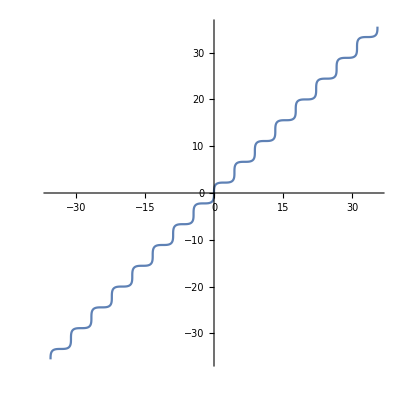

```mathematica
ParametricPlot[{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)},{x,-16 π,16 π}]
```

```mathematica
Composition[RotationTransform[ϕ],RotationTransform[θ]]
```

TransformationFunction[(Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ] | -Cos[ϕ] Sin[θ]-Cos[θ] Sin[ϕ] | 0
Cos[ϕ] Sin[θ]+Cos[θ] Sin[ϕ] | Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ] | 0
0 | 0 | 1)]

```mathematica
TransformationMatrix[TransformationFunction[{{Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ],-Cos[ϕ] Sin[θ]-Cos[θ] Sin[ϕ],0},{Cos[ϕ] Sin[θ]+Cos[θ] Sin[ϕ],Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ],0},{0,0,1}}]]
```

{{Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ],-Cos[ϕ] Sin[θ]-Cos[θ] Sin[ϕ],0},{Cos[ϕ] Sin[θ]+Cos[θ] Sin[ϕ],Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ],0},{0,0,1}}

```mathematica
MatrixForm[{{Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ],-Cos[ϕ] Sin[θ]-Cos[θ] Sin[ϕ],0},{Cos[ϕ] Sin[θ]+Cos[θ] Sin[ϕ],Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ],0},{0,0,1}}]
```

(Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ] | -Cos[ϕ] Sin[θ]-Cos[θ] Sin[ϕ] | 0
Cos[ϕ] Sin[θ]+Cos[θ] Sin[ϕ] | Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ] | 0
0 | 0 | 1)

```mathematica
Simplify@Composition[RotationTransform[ϕ],RotationTransform[θ]]
```

TransformationFunction[(Cos[θ+ϕ] | -Sin[θ+ϕ] | 0
Sin[θ+ϕ] | Cos[θ+ϕ] | 0
0 | 0 | 1)]

```mathematica
RotationTransform[θ][f[x]]==λ f[x]
```

TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)][f[x]]==λ f[x]

```mathematica
Simplify[RotationTransform[θ][f[x]]==λ f[x]]
```

λ f[x]==TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)][f[x]]

```mathematica
Solve[RotationTransform[θ][f[x]]==λ f[x],f[x]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)][f[x]]==λ f[x],f[x]]

```mathematica
Solve[RotationTransform[θ][f[x]]==λ f[x],λ]
```

{{λ→(TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)][f[x]])/f[x]}}

```mathematica
D[{t,t},t]
```

{1,1}

```mathematica
Normalize[{1,1}]
```

{1/(√2),1/(√2)}

```mathematica
Integrate[{1/(√2),1/(√2)},t]
```

{t/(√2),t/(√2)}

```mathematica
{t/(√2),t/(√2)}
```

```mathematica
(1/(√2))^2+(1/(√2))^2==1
```

True

```mathematica
D[{x[t],y[t]},t]
```

{x'[t],y'[t]}

```mathematica
Normalize[D[{x[t],y[t]},t]]
```

{x'[t]/(√(Abs[x'[t]]^2+Abs[y'[t]]^2)),y'[t]/(√(Abs[x'[t]]^2+Abs[y'[t]]^2))}

```mathematica
FullSimplify[
Normalize[D[{x[t],y[t]},t]], {x'[t],y'[t]}∈Reals]
```

{x'[t]/(√(x'[t]^2+y'[t]^2)),y'[t]/(√(x'[t]^2+y'[t]^2))}

```mathematica
Power[{x'[t]/(√(x'[t]^2+y'[t]^2)),y'[t]/(√(x'[t]^2+y'[t]^2))},2]
```

{x'[t]^2/(x'[t]^2+y'[t]^2),y'[t]^2/(x'[t]^2+y'[t]^2)}

```mathematica
Total[Power[{x'[t]/(√(x'[t]^2+y'[t]^2)),y'[t]/(√(x'[t]^2+y'[t]^2))},2]]
```

x'[t]^2/(x'[t]^2+y'[t]^2)+y'[t]^2/(x'[t]^2+y'[t]^2)

```mathematica
Total[Power[{x'[t]/(√(x'[t]^2+y'[t]^2)),y'[t]/(√(x'[t]^2+y'[t]^2))},2]]==1
```

x'[t]^2/(x'[t]^2+y'[t]^2)+y'[t]^2/(x'[t]^2+y'[t]^2)==1

```mathematica
DSolve[x'[t]^2/(x'[t]^2+y'[t]^2)+y'[t]^2/(x'[t]^2+y'[t]^2)==1,{x[t],y[t]},{t}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[x'[t]^2/(x'[t]^2+y'[t]^2)+y'[t]^2/(x'[t]^2+y'[t]^2)==1,{x[t],y[t]},{t}]

```mathematica
ExpandAll[x'[t]^2/(x'[t]^2+y'[t]^2)+y'[t]^2/(x'[t]^2+y'[t]^2)==1]
```

x'[t]^2/(x'[t]^2+y'[t]^2)+y'[t]^2/(x'[t]^2+y'[t]^2)==1

```mathematica
(x'[t]^2+y'[t]^2)/(x'[t]^2+y'[t]^2)==1
```

True

```mathematica
Simplify[x'[t]^2/(x'[t]^2+y'[t]^2)+y'[t]^2/(x'[t]^2+y'[t]^2)==1]
```

True

```mathematica
Trace[True]
```

{}

```mathematica
Trace[True[]]
```

{}

```mathematica
Trace[Simplify[x'[t]^2/(x'[t]^2+y'[t]^2)+y'[t]^2/(x'[t]^2+y'[t]^2)==1]]
```

{Simplify[x'[t]^2/(x'[t]^2+y'[t]^2)+y'[t]^2/(x'[t]^2+y'[t]^2)==1],True}

```mathematica
Composition[RotationTransform[θ],RotationTransform[ϕ]]
```

TransformationFunction[(Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ] | -Cos[ϕ] Sin[θ]-Cos[θ] Sin[ϕ] | 0
Cos[ϕ] Sin[θ]+Cos[θ] Sin[ϕ] | Cos[θ] Cos[ϕ]-Sin[θ] Sin[ϕ] | 0
0 | 0 | 1)]

```mathematica
Simplify[Composition[RotationTransform[θ],RotationTransform[ϕ]]]
```

TransformationFunction[(Cos[θ+ϕ] | -Sin[θ+ϕ] | 0
Sin[θ+ϕ] | Cos[θ+ϕ] | 0
0 | 0 | 1)]

```mathematica
TransformationMatrix[TransformationFunction[{{Cos[θ+ϕ],-Sin[θ+ϕ],0},{Sin[θ+ϕ],Cos[θ+ϕ],0},{0,0,1}}]]
```

{{Cos[θ+ϕ],-Sin[θ+ϕ],0},{Sin[θ+ϕ],Cos[θ+ϕ],0},{0,0,1}}

```mathematica
MatrixForm[{{Cos[θ+ϕ],-Sin[θ+ϕ],0},{Sin[θ+ϕ],Cos[θ+ϕ],0},{0,0,1}}]
```

(Cos[θ+ϕ] | -Sin[θ+ϕ] | 0
Sin[θ+ϕ] | Cos[θ+ϕ] | 0
0 | 0 | 1)

```mathematica
Composition[RotationTransform[π/4], TranslationTransform[{a,b}],ScalingTransform[{x,y}]]
```

TransformationFunction[(x/(√2) | -y/(√2) | a/(√2)-b/(√2)
x/(√2) | y/(√2) | a/(√2)+b/(√2)
0 | 0 | 1)]

```mathematica
Simplify[%]
```

TransformationFunction[(x/(√2) | -y/(√2) | (a-b)/(√2)
x/(√2) | y/(√2) | (a+b)/(√2)
0 | 0 | 1)]

```mathematica
Simplify[Composition[RotationTransform[π/4], TranslationTransform[{1,-1}],ScalingTransform[{2,2}]]]
```

TransformationFunction[(√2 | -√2 | √2
√2 | √2 | 0
0 | 0 | 1)]

```mathematica
TransformationFunction[({{√2, -√2, √2}, {√2, √2, 0}, {0, 0, 1}})][{x,x}]
```

{√2,2 √2 x}

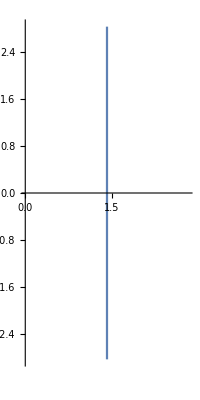

```mathematica
ParametricPlot[{√2,2 √2 x},{x,-1,1}]
```

```mathematica
TransformationFunction[({{√2, -√2, √2}, {√2, √2, 0}, {0, 0, 1}})][{x,Sin[x]}]
```

{√2+√2 x-√2 Sin[x],√2 x+√2 Sin[x]}

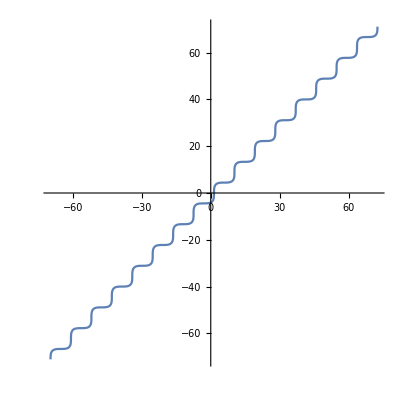

```mathematica
ParametricPlot[{√2+√2 x-√2 Sin[x],√2 x+√2 Sin[x]},{x,-16 π,16 π}]
```

```mathematica
RotationTransform[π/4]
```

TransformationFunction[(1/(√2) | -1/(√2) | 0
1/(√2) | 1/(√2) | 0
0 | 0 | 1)]

```mathematica
TransformationFunction[({{1/(√2), -1/(√2), 0}, {1/(√2), 1/(√2), 0}, {0, 0, 1}})][{x,Sin[x]}]
```

{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}

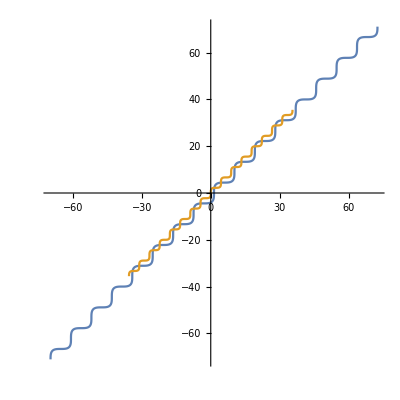

```mathematica
ParametricPlot[{
{√2+√2 x-√2 Sin[x],√2 x+√2 Sin[x]},
{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}},
{x,-16 π,16 π}]
```

```mathematica
ImageTransformation[-Graphics3D-, AffineTransform[({{1, 0.5, 0}, {0, 1, 0}, {0, 0, 1}})]]
```

-Graphics3D-

```mathematica
m=EulerMatrix[{π/4,π/3,(3 π)/4}];
```

```mathematica
Graphics3D[GeometricTransformation[Cuboid[],m]]
```

-Graphics3D-

```mathematica
Laplacian[f[x,y], {x,y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

```mathematica
RevolutionPlot3D[PDF[NormalDistribution[],t], {t, -3, 3}]
```

-Graphics3D-

```mathematica
BinormalDistribution[]
```

BinormalDistribution::argb: BinormalDistribution called with 0 arguments; between 1 and 3 arguments are expected.

BinormalDistribution[]

```mathematica
NormalDistribution[]
```

NormalDistribution[0,1]

```mathematica
BinormalDistribution[{1,1},{0,0}]
```

BinormalDistribution[{1,1},{0,0}]

```mathematica
PDF[BinormalDistribution[{1,1},{0,0}], {x,y}]
```

BinormalDistribution::corprm: Parameter {0,0} at position 2 in BinormalDistribution[{1,1},{0,0}] is expected to be greater than -1 and less than 1.

PDF[BinormalDistribution[{1,1},{0,0}],{x,y}]

```mathematica
PDF[BinormalDistribution[{1,1},{0,0}, 0], {x,y}]
```

BinormalDistribution::vrposln: The value {0,0} at position 2 in BinormalDistribution[{1,1},{0,0},0] is expected to be a length 2 list of positive numbers.

PDF[BinormalDistribution[{1,1},{0,0},0],{x,y}]

```mathematica
PDF[BinormalDistribution[{Subscript[μ,1],Subscript[μ,2]},{Subscript[σ,1],Subscript[σ,2]},ρ],{x,y}]
```

(ⅇ^(-((x-μ_1)^2/σ_1^2+(y-μ_2)^2/σ_2^2-(2 ρ (x-μ_1) (y-μ_2))/(σ_1 σ_2))/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ_1 σ_2)

```mathematica
PDF[BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]},ρ],{x,y}]
```

(ⅇ^(-((x-μ_1)^2/σ_1^2+(y-μ_2)^2/σ_2^2-(2 ρ (x-μ_1) (y-μ_2))/(σ_1 σ_2))/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ_1 σ_2)

```mathematica
PDF[BinormalDistribution[{μ,μ},{σ,σ},ρ],{x,y}]
```

(ⅇ^(-((x-μ)^2/σ^2+(y-μ)^2/σ^2-(2 (x-μ) (y-μ) ρ)/σ^2)/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ^2)

```mathematica
Simplify[(ⅇ^(-((x-μ)^2/σ^2+(y-μ)^2/σ^2-(2 (x-μ) (y-μ) ρ)/σ^2)/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ^2)]
```

(ⅇ^((x^2+y^2+2 y μ (-1+ρ)-2 μ^2 (-1+ρ)-2 x (μ+y ρ-μ ρ))/(2 (-1+ρ^2) σ^2)))/(2 π √(1-ρ^2) σ^2)

```mathematica
Out[180]/.ρ->0
```

(ⅇ^(-(x^2+y^2-2 x μ-2 y μ+2 μ^2)/(2 σ^2)))/(2 π σ^2)

```mathematica
FullSimplify[(ⅇ^(-(x^2+y^2-2 x μ-2 y μ+2 μ^2)/(2 σ^2)))/(2 π σ^2)]
```

(ⅇ^(-(x^2+y^2-2 (x+y) μ+2 μ^2)/(2 σ^2)))/(2 π σ^2)

```mathematica
PDF[BinormalDistribution[{μ,μ},{σ,σ},ρ],{x,y}]/.{μ->1,σ->0}
```

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Indeterminate

```mathematica
PDF[BinormalDistribution[{μ,μ},{σ,σ},ρ],{x,y}]
```

(ⅇ^(-((x-μ)^2/σ^2+(y-μ)^2/σ^2-(2 (x-μ) (y-μ) ρ)/σ^2)/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ^2)

```mathematica
PDF[BinormalDistribution[{μ,μ},{σ,σ},ρ],{x,y}]/.{μ->0,σ->1}
```

(ⅇ^(-(x^2+y^2-2 x y ρ)/(2 (1-ρ^2))))/(2 π √(1-ρ^2))

```mathematica
Simplify[(ⅇ^(-(x^2+y^2-2 x y ρ)/(2 (1-ρ^2))))/(2 π √(1-ρ^2))]
```

(ⅇ^((x^2+y^2-2 x y ρ)/(2 (-1+ρ^2))))/(2 π √(1-ρ^2))

```mathematica
PDF[BinormalDistribution[{μ,μ},{σ,σ},ρ],{x,y}]/.{μ->0,σ->1,ρ->0}
```

(ⅇ^(1/2 (-x^2-y^2)))/(2 π)

```mathematica
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(2 π),{x,-0.43907057974912933,0.439070576991095},{y,-0.439070576992762,0.43907057974746233}]
```

-Graphics3D-

```mathematica
Plot3D[(ⅇ^(1/2 (-x^2-y^2)))/(2 π), {x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Grad[(ⅇ^(1/2 (-x^2-y^2)))/(2 π),{x,y}]
```

{-(ⅇ^(1/2 (-x^2-y^2)) x)/(2 π),-(ⅇ^(1/2 (-x^2-y^2)) y)/(2 π)}

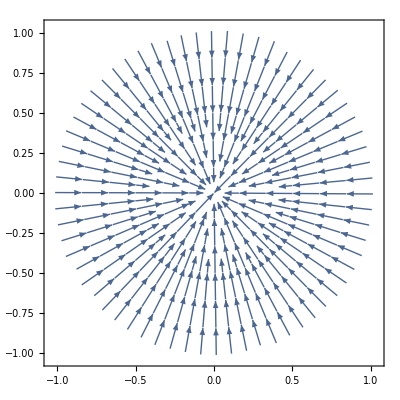

```mathematica
StreamPlot[{-(ⅇ^(1/2 (-x^2-y^2)) x)/(2 π),-(ⅇ^(1/2 (-x^2-y^2)) y)/(2 π)}, {x,y}∈Disk[]]
```

```mathematica
Div[(ⅇ^(1/2 (-x^2-y^2)))/(2 π), {x,y}]
```

Div::sclr: The scalar expression (ⅇ^(1/2 (-x^2-y^2)))/(2 π) does not have a divergence.

(ⅇ^(1/2 (-x^2-y^2)))/(2 π){x,y}

```mathematica
Curl[(ⅇ^(1/2 (-x^2-y^2)))/(2 π),{x,y}]
```

{(ⅇ^(1/2 (-x^2-y^2)) y)/(2 π),-(ⅇ^(1/2 (-x^2-y^2)) x)/(2 π)}

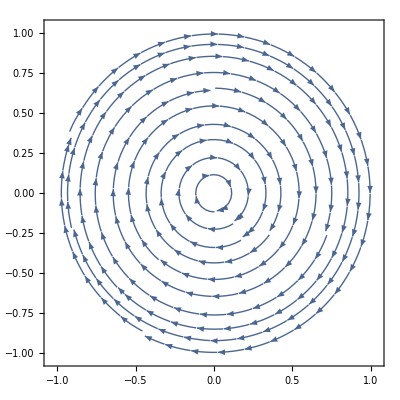

```mathematica
StreamPlot[{(ⅇ^(1/2 (-x^2-y^2)) y)/(2 π),-(ⅇ^(1/2 (-x^2-y^2)) x)/(2 π)}, {x,y}∈Disk[]]
```

```mathematica
Curl[{1,3 x^2},{x,y}]
```

6 x

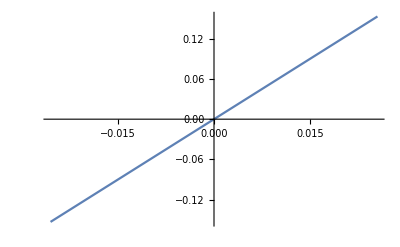

```mathematica
Plot[6 x,{x,-0.025500000000000002,0.025500000000000002}]
```

```mathematica
Laplacian[(ⅇ^(1/2 (-x^2-y^2)))/(2 π), {x,y}]
```

-(ⅇ^(1/2 (-x^2-y^2)))/π+(ⅇ^(1/2 (-x^2-y^2)) x^2)/(2 π)+(ⅇ^(1/2 (-x^2-y^2)) y^2)/(2 π)

```mathematica
Plot3D[-(ⅇ^(1/2 (-x^2-y^2)))/π+(ⅇ^(1/2 (-x^2-y^2)) x^2)/(2 π)+(ⅇ^(1/2 (-x^2-y^2)) y^2)/(2 π),{x,-0.43892152126807016,0.4389215210579016},{y,-0.4389215210579782,0.43892152126799355}]
```

-Graphics3D-

```mathematica
Plot3D[-(ⅇ^(1/2 (-x^2-y^2)))/π+(ⅇ^(1/2 (-x^2-y^2)) x^2)/(2 π)+(ⅇ^(1/2 (-x^2-y^2)) y^2)/(2 π),{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Plot3D[-(ⅇ^(1/2 (-x^2-y^2)))/π+(ⅇ^(1/2 (-x^2-y^2)) x^2)/(2 π)+(ⅇ^(1/2 (-x^2-y^2)) y^2)/(2 π),{x,y}∈Disk[{0,0},2]]
```

-Graphics3D-

```mathematica
Laplacian[f[x,y],{x,y}]==f[x,y]
```

f^(0,2)[x,y]+f^(2,0)[x,y]==f[x,y]

```mathematica
DSolve[Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y]==f[x,y],{f[x,y],f[x,y]},{x,y}]
```

DSolve[f^(0,2)[x,y]+f^(2,0)[x,y]==f[x,y],{f[x,y],f[x,y]},{x,y}]

```mathematica
Laplacian[f[x],{x}]==f[x]
```

f''[x]==f[x]

```mathematica
DSolve[f''[x]==f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^x C[1]+ⅇ^-x C[2]}}

```mathematica
-∫_0^1 x Log[x]ⅆx
```

1/4

```mathematica
Kurtosis[NormalDistribution[]]
```

3